# Neutron induced Migdal events in xenon

This notebook calculates the rate of Migdal events due to nuclear recoils of low energy neutrons in a detector with xenon and argon targets.

Gray (initialization) cells can/should be evaluated automatically
Red cells are computations (ones that usually take more than a few seconds)
Blue cells create plots
Purple cells create output files

## Constants

All units are in GeV unless otherwise explicitly noted

```mathematica
GeV=1;
MeV=10^-3 GeV;
keV=10^-6 GeV;
eV=10^-9 GeV;
ℏc=0.19732698;(*GeV fm*)
𝒸=2.997925 10^8;(*m/s*)
α=1/137.036;
e=0.30282212;

(*particle masses*)
mn=0.93956542052; (*neutron mass*)
amu=mn/1.00727; (*atomic mass unit*)
mp=0.93827; (*proton mass*)
me=0.000511; (*electron mass*)

(*Useful units*)
Centimeter= 1/ℏc 10^13(*GeV^-1*);
Second= 𝒸 10^2 Centimeter;
Kilogram=𝒸^2/(1.602 10^-19/eV);
KilogramDay= (1 Kilogram)(24 3600 Second);
cm2s=(Centimeter^2/(1(*cm^2*)))(Second/(1(*s*)));
μ[x_,y_]:=(x y)/(x+y)
```

## Kinematics

To make sure the neutrons are sufficiently below threshold we will assume a quasi-monoenergetic source with E_n = 17 keV, like that described in  1403.1285, this gives a maximum nuclear recoil of E_R=0.5 keV

### Elastic scattering

-Graphics-

En = incoming neutron energy
Er  = nuclear recoil energy
mT= nuclear target mass
mn = neutron mass

Energy conservation:
En = En’ + Er

Momentum conservation in x and y:
√(2 mn En)                = √(2 mn En') cosθ + √(2 mT Er)cosϕ 
√(2 mn En') sinθ   = √(2 mT Er)sinϕ  

Second line gives:
cos^2(ϕ)==1-(mn (En-Er))/(Er mT)sin^2(θ)

```mathematica
Solve[ {√(2 MN En)==√(2mT Er)(√(1-(2 MN (En-Er))/(2mT Er)Sin[θ]^2))+√(2MN (En-Er))Cos[θ]},Er]//FullSimplify[#,Assumptions->{En>0,MN>0,mT>0}]&
```

{{Er→(En MN (MN+2 mT-MN Cos[2 θ]-√2 √(Cos[θ]^2 (-MN^2+2 mT^2+MN^2 Cos[2 θ]))))/(MN+mT)^2},{Er→(En MN (MN+2 mT-MN Cos[2 θ]+√2 √(Cos[θ]^2 (-MN^2+2 mT^2+MN^2 Cos[2 θ]))))/(MN+mT)^2}}

```mathematica
ER[En_,MN_,mT_,θ_]:=(En MN (MN+2 mT-MN Cos[2 θ]-√2 Cos[θ] √(-MN^2+2 mT^2+MN^2 Cos[2 θ])))/(MN+mT)^2
```

```mathematica
Solve[ {√(2 MN En)==√(2mT Er)√(1-(MN (En-Er))/(mT Er)(1-Cos[θ]^2))+√(2MN (En-Er))Cos[θ]},Cos[θ]]//FullSimplify
```

{{Cos[θ]→(2 En MN-Er (MN+mT))/(2 √(En MN) √((En-Er) MN))}}

```mathematica
cosθ[Er_,En_,MN_,mT_]:=(2 En -Er (1+mT/MN))/(2 √(En (En-Er)))
```

```mathematica
D[(2 En -Er (1+mT/MN))/(2 √(En (En-Er))),Er]//Simplify
```

(En (-2 En mT+Er (MN+mT)))/(4 (En (En-Er))^(3/2) MN)

```mathematica
dcosθdEr[Er_,En_,MN_,mT_]:=(En (-2 En mT+Er (MN+mT)))/(4 (En (En-Er))^(3/2) MN)
```

Maximum recoil occurs when θ = π:

```mathematica
ER[En,MN,mT,π]//Simplify[#,Assumptions->mT>0]&
```

(4 En MN mT)/(MN+mT)^2

```mathematica
ERmax[En_,MN_,mT_] = (4 En μ[MN,mT]^2)/(MN mT);
```

```mathematica
ERmax[En_,MN_,mT_]
```

(4 En_ MN_ mT_)/(MN_+mT_)^2

#### Approximation

Or approximately (taking mn/mT << 1):

```mathematica
ERapprox[En_,MN_,mT_,θ_]:=2En MN mT(1-Cos[θ])/(MN+mT)^2
```

```mathematica
Solve[Er==2En MN mT(1-Cos[θ])/(MN+mT)^2,Cos[θ]]
```

{{Cos[θ]→(-Er MN^2+2 En MN mT-2 Er MN mT-Er mT^2)/(2 En MN mT)}}

```mathematica
cosθapprox[Er_,En_,MN_,mT_]:=(-Er MN^2+2 En MN mT-2 Er MN mT-Er mT^2)/(2 En MN mT)
```

```mathematica
D[(-Er MN^2+2 En MN mT-2 Er MN mT-Er mT^2)/(2 En MN mT),Er]
```

(-MN^2-2 MN mT-mT^2)/(2 En MN mT)

```mathematica
dcosθdErApprox[Er_,En_,MN_,mT_]:=(-MN^2-2 MN mT-mT^2)/(2 En MN mT)
```

#### Kinematic plots

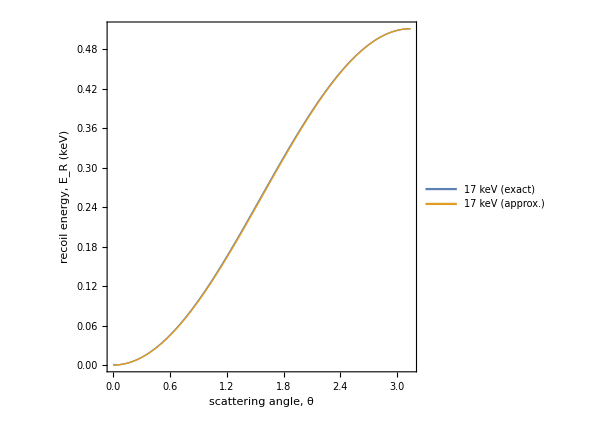

```mathematica
Plot[
{ER[17,mn 10^6,131 mn 10^6,θ],
ERapprox[17,mn 10^6,131 mn 10^6,θ]},
{θ,0,π},
PlotLegends->Legend[{"17 keV (exact)","17 keV (approx.)"},Position->"Left"],
FrameLabel->{"scattering angle, θ","recoil energy, E_R (keV)"}]
```

The approximation is better than 2% accurate everywhere:

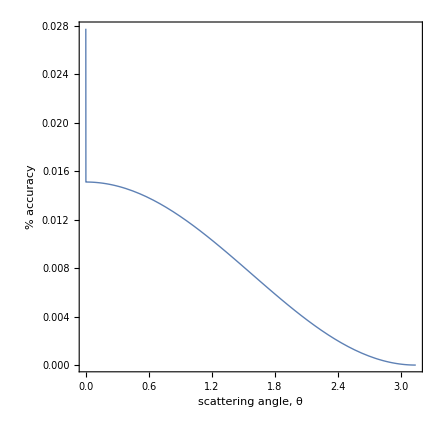

```mathematica
Plot[
{(ER[10^-5,1,131,θ]-ERapprox[10^-5,1,131,θ])/ER[10^-5,1,131,θ]},
{θ,0,π},
FrameLabel->{"scattering angle, θ","% accuracy"}]
```

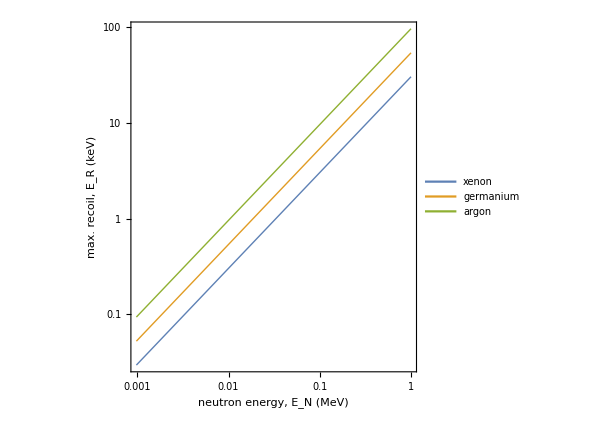

```mathematica
LogLogPlot[
{ERmax[EnMeV 10^-3,mn,131.3amu] 10^6(*keV*),
ERmax[EnMeV 10^-3,mn,73amu] 10^6(*keV*),
ERmax[EnMeV 10^-3,mn,40amu] 10^6(*keV*)},
{EnMeV,0,1},
FrameLabel->{"neutron energy, E_N (MeV)","max. recoil, E_R (keV)"},
FrameTicks->{LogTicks[10^-3,100],LogTicks[10^-3,10]},
PlotLegends->Legend[{"xenon","germanium","argon"},Position->{.25,.8}]]
```

### Inelastic scattering

For inelastic scattering use the same variables as before with the addition of:

EM = excitation energy of atom (this will be electron kinetic + electronic binding energy)

Energy conservation:
En = En’ + Er + EM

Momentum conservation in x and y (ignoring electron momentum):
√(2 mn En)                = √(2 mn En') cosθ + √(2 mT Er)cosϕ 
√(2 mn En') sinθ   = √(2 mT Er)sinϕ

Second line gives:
cos^2(ϕ)==1-(mn (En-Er-EM))/(Er mT)sin^2(θ)

```mathematica
Solve[ {√(2 MN En)==√(2mT Er)(√(1-(2 MN (En-Er-EM))/(2mT Er)(1-Cos[θ]^2)))+√(2MN (En-Er-EM))Cos[θ]},Cos[θ]]//FullSimplify
```

{{Cos[θ]→-((EM-2 En+Er) MN+Er mT)/(2 √(En MN) √(-(EM-En+Er) MN))}}

```mathematica
cosθi[Er_?NumericQ,En_?NumericQ,EM_?NumericQ,MN_?NumericQ,mT_?NumericQ]:=((2 En-EM-Er) MN-Er mT)/(2 √(En (En-EM-Er)) MN)
```

```mathematica
D[((2 En-EM-Er) MN-Er mT)/(2 √(En (En-EM-Er)) MN),Er]//FullSimplify
```

(En (-2 En mT+Er (MN+mT)+EM (MN+2 mT)))/(4 (-En (EM-En+Er))^(3/2) MN)

```mathematica
dcosθdEr[Er_?NumericQ,En_?NumericQ,EM_?NumericQ,MN_?NumericQ,mT_?NumericQ]:=(En (-2 En mT+Er (MN+mT)+EM (MN+2 mT)))/(4 (-En (EM-En+Er))^(3/2) MN);
```

Find max inelastic energy as function of Er:

```mathematica
Solve[Cos[0]==-((EM-2 En+Er) MN+Er mT)/(2 √(En MN) √(-(EM-En+Er) MN)),EM]//Simplify[#,Assumptions->{MN>0,mT>0,Er>0}]&
```

{{EM→-(2 √(En Er MN mT)+Er (MN+mT))/MN},{EM→(2 √(En Er MN mT)-Er (MN+mT))/MN}}

```mathematica
EemMaxER[Er_?NumericQ,En_?NumericQ,MN_?NumericQ,MT_?NumericQ]:=2 √(En Er MT/MN)-Er (MT+MN)/MN
```

Find Er which maximises EM:

```mathematica
erMaxEM=Solve[D[(2 √(En Er MN mT)-Er (MN+mT))/MN,Er]==0,Er][[1]]
```

{Er→(En MN mT)/(MN+mT)^2}

```mathematica
(2 √(En Er MN mT)-Er (MN+mT))/MN/.erMaxEM//Simplify[#,Assumptions->{MN>0,mT>0,Er>0,En>0}]&
```

(En mT)/(MN+mT)

```mathematica
EemMax[En_,MN_,mT_]= (μ[mT,MN]En)/MN;
```

Limits:

```mathematica
Solve[Cos[θ]==-((EM-2 En+Er) MN+Er mT)/(2 √(En MN) √(-(EM-En+Er) MN)),Er]/.θ->π//FullSimplify[#,Assumptions->{En>0,MN>0,mT>0}]&
```

{{Er→-(MN (-2 En mT+EM (MN+mT)+2 √(En mT (En mT-EM (MN+mT)))))/(MN+mT)^2},{Er→(MN (-EM (MN+mT)+2 (En mT+√(En mT (En mT-EM (MN+mT))))))/(MN+mT)^2}}

```mathematica
ErMin[En_?NumericQ,EM_?NumericQ,MN_?NumericQ,mT_?NumericQ]:=If[EemMax[En,MN,mT]>EM,-(MN (-2 En mT+EM (MN+mT)+2 √(En mT (En mT-EM (MN+mT)))))/(MN+mT)^2,10^100];
ErMax[En_?NumericQ,EM_?NumericQ,MN_?NumericQ,mT_?NumericQ]:=If[EemMax[En,MN,mT]>EM,(MN (-EM (MN+mT)+2 (En mT+√(En mT (En mT-EM (MN+mT))))))/(MN+mT)^2,10^100];
```

#### Inelastic kinematics plots

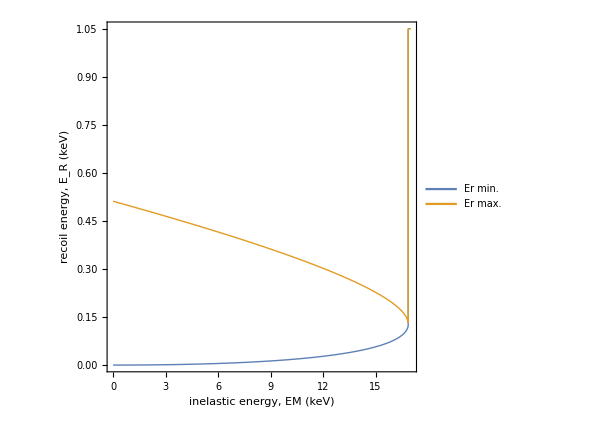

```mathematica
Plot[
{ErMin[17,EM,mn 10^6,131 mn 10^6],
ErMax[17,EM,mn 10^6,131 mn 10^6]},
{EM,0,17},
PlotLegends->Legend[{"Er min.","Er max."},Position->"Right"],
FrameLabel->{"inelastic energy, EM (keV)","recoil energy, E_R (keV)"}]
```

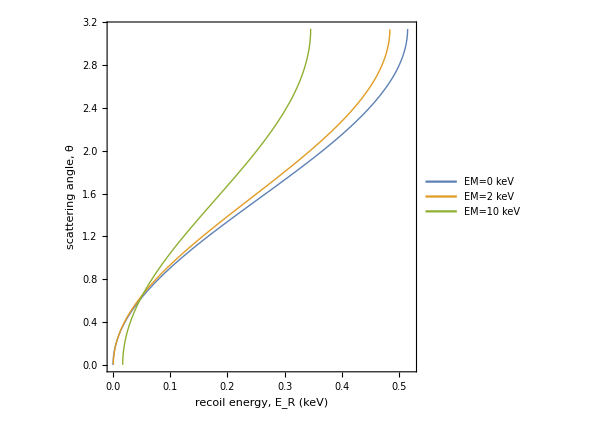

```mathematica
Plot[{ArcCos[cosθi[Er 10^-6,17 10^-6,0,mn,131amu]],cosθi[Er 10^-6,17 10^-6,2 10^-6,mn,131amu]//ArcCos,cosθi[Er 10^-6,17 10^-6,10 10^-6,mn,131amu]//ArcCos},{Er,0,.52},PlotLegends->Legend[{"EM=0 keV","EM=2 keV","EM=10 keV"},Position->"Left"],FrameLabel->{"recoil energy, E_R (keV)","scattering angle, θ"}]
```

## Neutron scattering cross sections

### Import cross sections

Values from NIST:

```mathematica
isotopesXe={"xe124","xe126","xe128","xe129","xe130","xe131","xe132","xe134","xe136"};
isotopesA={124,126,128,129,130,131,132,134,136};
isoFrac={0.000952,0.00089,.019102,.264006,.04071,.212324,.269086,.104357,.088573};
MtXe=131.293amu;
MtAr=39.948amu;
```

Import data from JENDL

Xenon elastic:

```mathematica
NotebookDirectory[]//SetDirectory;
rawCSdat=Table[Import["data/"<>isotopesXe[[ii]]<>"_elastic.txt","Table"]
,{ii,1,Length[isotopesXe]}];
```

Xenon capture:

```mathematica
rawNCCSdat=Table[Import["data/"<>isotopesXe[[ii]]<>"_capture.txt","Table"]
,{ii,1,Length[isotopesXe]}];
```

Argon elastic:

```mathematica
rawCSdatAR=Import["data/ar40_300K_elastic.txt","Table"];
```

Argon capture:

```mathematica
rawNCCSdatAR=Import["data/ar40_300K_capture.txt","Table"];
```

Extract data and create interpolation object:

```mathematica
xeCS=Table[Join[rawCSdat[[ii,All;;-2,{1,2}]],rawCSdat[[ii,All;;-2,{3,4}]],rawCSdat[[ii,All;;-2,{5,6}]]]//Sort[#,#1[[1]]<#2[[1]]&]&//DeleteDuplicatesBy[#,First]&//Interpolation[#,InterpolationOrder->1]&
,{ii,1,Length[isotopesXe]}];
xeNCCS=Table[Join[rawNCCSdat[[ii,All;;-2,{1,2}]],rawNCCSdat[[ii,All;;-2,{3,4}]],rawNCCSdat[[ii,All;;-2,{5,6}]]]//Sort[#,#1[[1]]<#2[[1]]&]&//DeleteDuplicatesBy[#,First]&//Interpolation[#,InterpolationOrder->1]&
,{ii,1,Length[isotopesXe]}];
```

```mathematica
arCS=Join[rawCSdatAR[[All;;-2,{1,2}]],rawCSdatAR[[All;;-2,{3,4}]],rawCSdatAR[[All;;-2,{5,6}]]]//Sort[#,#1[[1]]<#2[[1]]&]&//DeleteDuplicatesBy[#,First]&//Interpolation[#,InterpolationOrder->1]&;
arNCCS=Join[rawNCCSdatAR[[All;;-2,{1,2}]],rawNCCSdatAR[[All;;-2,{3,4}]],rawNCCSdatAR[[All;;-2,{5,6}]]]//Sort[#,#1[[1]]<#2[[1]]&]&//DeleteDuplicatesBy[#,First]&//Interpolation[#,InterpolationOrder->1]&;
```

Define function which returns cross sections in cm^2, averaged over isotopes:

```mathematica
xeAvgCScm2[EReV_]:=Sum[isoFrac[[ii]]xeCS[[ii]][EReV] 10^-24,{ii,1,Length[isotopesXe]}]
xeAvgNCCScm2[EReV_]:=Sum[isoFrac[[ii]]xeNCCS[[ii]][EReV] 10^-24,{ii,1,Length[isotopesXe]}]
```

```mathematica
arCScm2[EReV_]:=arCS[EReV] 10^-24;
arNCCScm2[EReV_]:=arNCCS[EReV] 10^-24;
```

#### Cross section comparison plots

Isotope averaged cross sections:

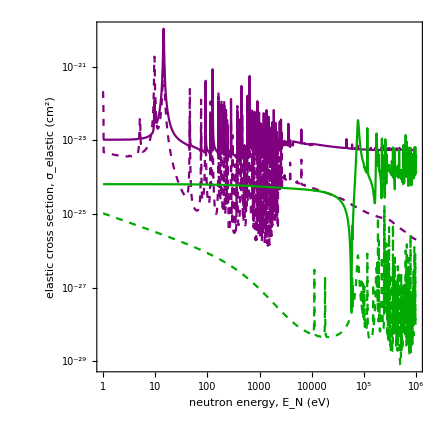

```mathematica
CSplot=LogLogPlot[{xeAvgCScm2[er],xeAvgNCCScm2[er],arCScm2[er],arNCCScm2[er]},{er,1,10^6},PlotRange->All,
PlotStyle->{Purple,{Purple,Dashed},Darker[Green],{Darker[Green],Dashed}},
FrameLabel->{"neutron energy, E_N (eV)","elastic cross section, σ_elastic (cm^2)"},
FrameTicks->{LogTicks[10^-24,10^-19],LogTicks[10^-3,10^8,2]}]
```

Ratio of elastic to neutron capture cross sections in most relevant region:

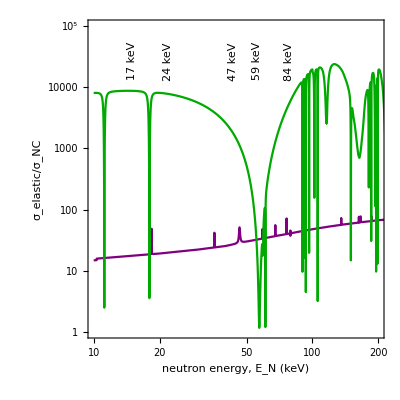

```mathematica
ratioCSplot=LogLogPlot[{xeAvgCScm2[er 10^3]/xeAvgNCCScm2[er 10^3],arCScm2[er 10^3]/arNCCScm2[er 10^3]},{er,10,10^3},PlotPoints->10^3,
FrameLabel->{"neutron energy, E_N (keV)","σ_elastic/σ_NC"},FrameTicks->{LogTicks[10^-1,10^5],LogTicks[10^-1,10^5,1]},
PlotStyle->{Purple,Darker[Green]},
GridLines->{{17,24,47,59,82},None},PlotRange->{{10,200},{1,10^5}},
Epilog->{Style[Text["17 keV",Scaled[{.15,.87}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],Style[Text["24 keV",Scaled[{.27,.87}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["47 keV",Scaled[{.49,.87}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["59 keV",Scaled[{.57,.87}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["84 keV",Scaled[{.68,.87}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5]}]
```

#### Check temperature dependence

```mathematica
rawCSdat300K=Import["data/xe131_elastic.txt","Table"];
```

```mathematica
xeCS300K=Join[rawCSdat300K[[All;;-2,{1,2}]],rawCSdat300K[[All;;-2,{3,4}]],rawCSdat300K[[All;;-2,{5,6}]]]//Sort[#,#1[[1]]<#2[[1]]&]&//DeleteDuplicatesBy[#,First]&//Interpolation[#,InterpolationOrder->1]&;
```

```mathematica
rawCSdat0K=Import["data/xe131_0K_elastic.txt","Table"];
```

```mathematica
xeCS0K=Join[rawCSdat0K[[All;;-2,{1,2}]],rawCSdat0K[[All;;-2,{3,4}]],rawCSdat0K[[All;;-2,{5,6}]]]//Sort[#,#1[[1]]<#2[[1]]&]&//DeleteDuplicatesBy[#,First]&//Interpolation[#,InterpolationOrder->1]&;
```

```mathematica
xeCS0K[.01]/xeCS300K[.01]
```

0.989912

```mathematica
xeCS0K[10000]/xeCS300K[10000]
```

1.

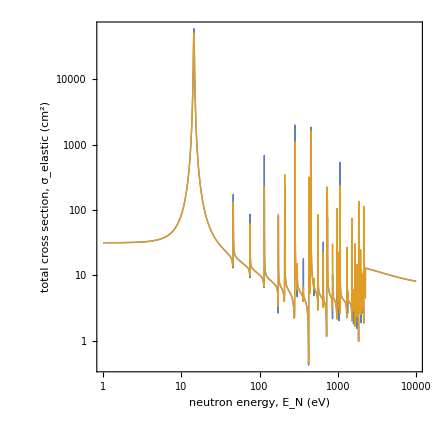

```mathematica
LogLogPlot[{xeCS0K[er],xeCS300K[er]},{er,1,10^4},PlotRange->All,FrameLabel->{"neutron energy, E_N (eV)","total cross section, σ_elastic (cm^2)"},FrameTicks->{LogTicks[10^-24,10^-19],LogTicks[10^-3,10^8,2]}]
```

### Mean free path

Mean free path in liquid xenon with density 3g/mL:

```mathematica
nAr=1.4g/mL * ((6.02 10^23)/(40g))*((1mL)/(1 cm^3));
nXe=3g/mL * ((6.02 10^23)/(131.3g))*((1mL)/(1 cm^3));
```

Beam energy to consider:

```mathematica
Eneutron=17 keV;
```

Functions for mean free path and

```mathematica
MFPxe[En_]:=(xeAvgCScm2[En/eV] cm^2 nXe)^-1;
MFPar[En_]:=(arCS[En/eV] 10^-24 cm^2 nAr)^-1;
```

Differential probability of interacting at x and cumulative prob (for xenon detector because that’s the one we do a detailed simulation of):

```mathematica
dPdx[x_,en_:Eneutron]=1/MFPxe[en] Exp[-x cm/MFPxe[en]];
prob[X_,en_:Eneutron]=Integrate[dPdx[xi,en]cm,{xi,0,X}];
```

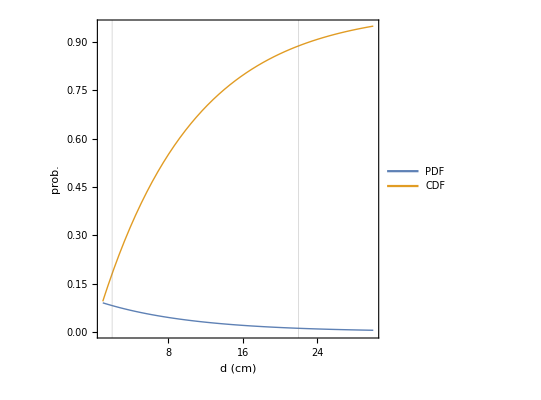

```mathematica
Plot[{dPdx[x]cm,prob[x]},{x,1,30},
FrameLabel->{"d (cm)","prob."},
PlotLegends->Legend[{"PDF","CDF"},Position->"Left"],
GridLines->{{2,22},None}]
```

Imagine a fiducial region with 2cm of xenon self-shielding

```mathematica
Integrate[dPdx[xi]cm,{xi,2,22}]
```

0.707665

Conclusion: a 20cm fiducial region will capture ~70% of events

### Cross section plot for paper

```mathematica
csPlotTicksXe=
{{LogTicks[10^-25,10^-19]⟦1⟧,
Join[Table[{(10^x cm^3 nXe)^-1,Superscript[10,x]},{x,-3,3,1}],Table[{(y 10^x cm^3 nXe)^-1,Null,{0.006,0}},{x,-2,2},{y,2,9}]//Flatten[#,1]&]},
{LogTicks[10^-1,10^5,1]⟦1⟧,
Join[Table[{(mn 131.3amu 10^x)/(4 μ[mn,131.3amu]^2),Superscript[10,x]},{x,-2,2}],Table[{y 10^x (mn 131.3amu)/(4 μ[mn,131.3amu]^2),Null,{0.006,0}},{x,-2,3},{y,2,9}]//Flatten[#,1]&]}};
```

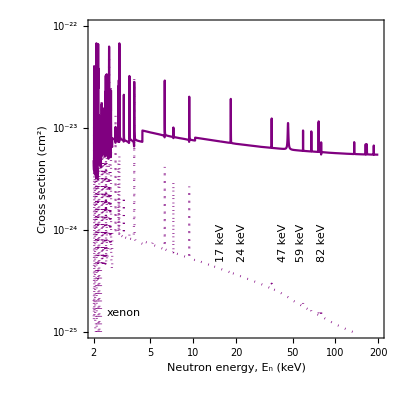

```mathematica
elasticCSplotXe=LogLogPlot[{xeAvgCScm2[er 10^3],xeAvgNCCScm2[er 10^3]},{er,2,2 10^2},PlotPoints->10000,
FrameLabel->{{"Cross section (cm^2)","Mean free path (cm)"},{"Neutron energy, E_n (keV)","Maximum E_R (keV)"}},
FrameTicks->csPlotTicksXe,PlotStyle->{Purple,{Purple,Dotted}},
GridLines->{{17,24,47,59,82},None},PlotRange->{{2,200},{10^-25,10^-22}},
Epilog->{Inset[Framed[Style["xenon",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.12,.08}]],Style[Text["17 keV",Scaled[{.45,.3}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],Style[Text["24 keV",Scaled[{.52,.3}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["47 keV",Scaled[{.66,.3}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["59 keV",Scaled[{.72,.3}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["82 keV",Scaled[{.79,.3}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5]}]
```

```mathematica
csPlotTicksAr=
{{LogTicks[10^-29,10^-19]⟦1⟧,
Join[Table[{(10^x nAr cm^3)^-1,Superscript[10,x]},{x,-2,6,1}],Table[{(y 10^x nAr cm^3)^-1,Null,{0.006,0}},{x,-3,8},{y,2,9}]//Flatten[#,1]&]},
{LogTicks[10^-1,10^5,1]⟦1⟧,
Join[Table[{(mn 40amu 10^x)/(4 μ[mn,40amu]^2),Superscript[10,x]},{x,-2,2}],Table[{y 10^x (mn 40amu)/(4 μ[mn,40amu]^2),Null,{0.006,0}},{x,-2,3},{y,2,9}]//Flatten[#,1]&]}};
```

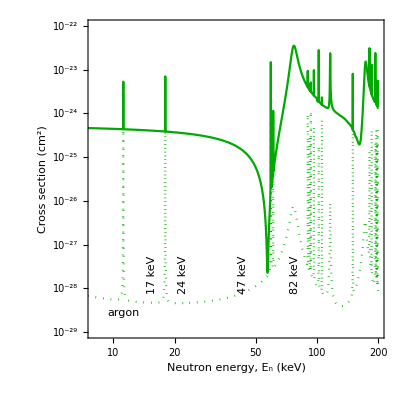

```mathematica
elasticCSplotAr=LogLogPlot[{arCScm2[er 10^3],arNCCScm2[er 10^3]},{er,1,2 10^2},PlotPoints->10000,
FrameLabel->{{"Cross section (cm^2)","Mean free path (cm)"},{"Neutron energy, E_n (keV)","Maximum E_R (keV)"}},
FrameTicks->csPlotTicksAr,PlotStyle->{Darker[Green],{Darker[Green],Dotted}},
GridLines->{{17,24,47,59,82},None},PlotRange->{{8,200},{10^-29,10^-22}},
Epilog->{Style[Text["17 keV",Scaled[{.215,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],Style[Text["24 keV",Scaled[{.32,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["47 keV",Scaled[{.525,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["82 keV",Scaled[{.7,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],Inset[Framed[Style["argon",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.12,.08}]]}]
```

```mathematica
Export["figures/fig_ar_neutron_cs.pdf",elasticCSplotAr];
Export["figures/fig_xe_neutron_cs.pdf",elasticCSplotXe];
```

### Beam profile

Import beam profile from arXiv:nucl-ex/0701011

```mathematica
beamDat=Import["data/beam_profile.csv"];
```

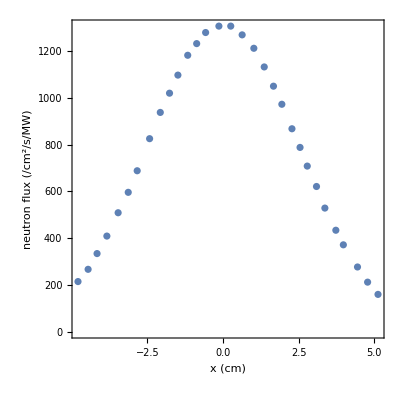

```mathematica
ListPlot[beamDat,
FrameLabel->{"x (cm)","neutron flux (/cm^2/s/MW)"}]
```

```mathematica
beamProf=beamDat//Interpolation;
```

```mathematica
totFlux=2π NIntegrate[beamProf[r]r,{r,0,4.2}]
```

39158.5

```mathematica
totFlux*3600
```

1.40971×10^8

Define a similar beam:

```mathematica
beamFit=FindFit[beamDat,a Exp[-(r-μi)^2/(2 σ^2)],{a,μi,σ},r]
```

{a→1311.24,μi→0.00262071,σ→2.51153}

```mathematica
FWHM=2.355σ/.beamFit
```

5.91465

We will assume a slightly higher peak flux to get a nice round number at the end:

```mathematica
1.11a/.beamFit
```

1455.48

```mathematica
totFlux= 2π NIntegrate[1.11a Exp[-(r-μi)^2/(2 σ^2)]r/.beamFit,{r,0,20}]
```

57760.5

How much is captured by our fiducial volume:

```mathematica
totCapturedFlux= NIntegrate[1.11a Exp[-((√(zz^2+y^2)-μi)^2)/(2 σ^2)]/.beamFit,{zz,-6,6},{y,-10,10}]
```

56779.

```mathematica
totCapturedFlux/totFlux
```

0.983008

What is the average flux presented:

```mathematica
avgFlux=totCapturedFlux/(12 20)
```

236.579

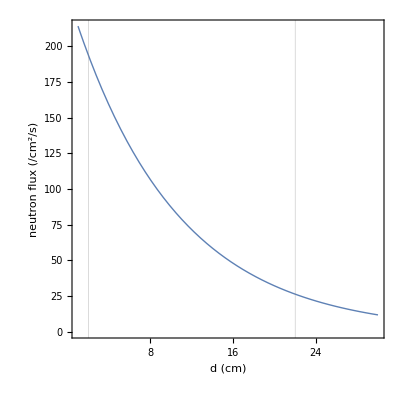

```mathematica
Plot[{avgFlux(1-prob[x])},{x,1,30},
FrameLabel->{"d (cm)","neutron flux (/cm^2/s)"},
GridLines->{{2,22},None}]
```

Depth of fiducial region changes across detector, so we capture this fraction of events:

```mathematica
1/20 NIntegrate[dPdx[x]cm,{y,-10,10},{x,2,2+2 √(10^2-y^2)}]
```

0.627023

The average flux across the detector is then:

```mathematica
depthAvgFlux=avgFlux/20 NIntegrate[(1-prob[x])/(2 √(10^2-y^2)),{y,-10,10},{x,2,2+2 √(10^2-y^2)}]
```

100.32

We will assume a baseline flux of 100 neutrons/cm^2/s (averaged over fiducial volume)

```mathematica
Φreactor=100/Centimeter^2/Second;
```

### Angular distribution of neutron scatter

Note that the angular distribution given by JENDL is in the CM frame:

```mathematica
cosθCMtocosθLab[cosθcm_,A_]:=(1+A cosθcm)/(√(1+A^2+2 A cosθcm))
cosθLabToCosθCM[cosθl_,A_]:=1/A (1-cosθl^2+cosθl √(A^2 +cosθl^2))
```

```mathematica
ang10=Table[Import["data/"<>isotopesXe[[ii]]<>"_ang10keV.txt","Table"]//Flatten//Prepend[#,1]&,{ii,1,Length[isotopesXe]}];
ang20=Table[Import["data/"<>isotopesXe[[ii]]<>"_ang20keV.txt","Table"]//Flatten//Prepend[#,1]&,{ii,1,Length[isotopesXe]}];
```

```mathematica
ang10ar=Import["data/ar40_300K_ang10keV.txt","Table"]//Flatten//Prepend[#,1]&;
ang25ar=Import["data/ar40_300K_ang25keV.txt","Table"]//Flatten//Prepend[#,1]&;
```

```mathematica
f10=Table[Plus@@Table[(2ii+1)/2 ang10[[jj,ii+1]]LegendreP[ii,x],{ii,0,40}]//Simplify,{jj,1,Length[isotopesXe]}];
f20=Table[Plus@@Table[(2ii+1)/2 ang20[[jj,ii+1]]LegendreP[ii,x],{ii,0,40}]//Simplify,{jj,1,Length[isotopesXe]}];
```

```mathematica
f10ar=Plus@@Table[(2ii+1)/2 ang10ar[[ii+1]]LegendreP[ii,x],{ii,0,Length[ang10ar]-1}]//Simplify;
f25ar=Plus@@Table[(2ii+1)/2 ang25ar[[ii+1]]LegendreP[ii,x],{ii,0,Length[ang25ar]-1}]//Simplify;
```

Interpolate between the angular distributions and change to lab frame:

```mathematica
f17[cosθl_,ii_]:=(.7f20[[ii]]+.3f10[[ii]])/.x->cosθLabToCosθCM[cosθl,isotopesA[[ii]]]
```

```mathematica
y==(y22-y11)/(x22-x11)x+(-x22 y11+x11 y22)/(x11-x22)/.{x11->10,x22->25,x->17}//Simplify
```

15 y==8 y11+7 y22

```mathematica
f17ar[cosθl_]:=(7/15 f25ar+8/15 f10ar)/.x->cosθLabToCosθCM[cosθl,40]
```

These are normalized functions:

```mathematica
NIntegrate[f17[x,2],{x,-1,1}]
```

1.00045

```mathematica
NIntegrate[f17ar[x],{x,-1,1}]
```

0.999977

This is used to define the differential cross section:
  σ_tot=∫σ_tot f(cosθ)ⅆcosθ
dσ/dcosθ≡ σ_tot f(cosθ)
σ_tot=(∫^1)_-1 dσ/dcosθ ⅆcosθ
Note the integration limits:
σ_tot=(∫^EMIN)_EMAX dσ/dcosθ dcosθ/dE_r ⅆ E_r
therefore define:
dσ/dE_r≡ σ_tot f(cosθ)(- dcosθ/dE_r)

#### Angular dist plot

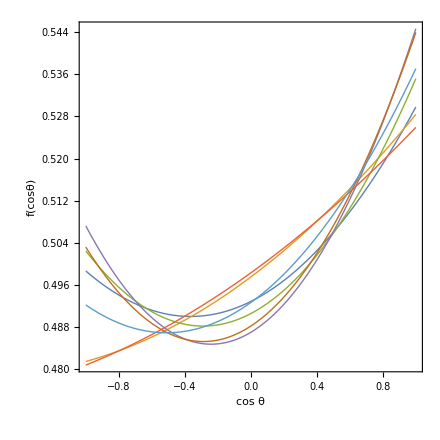

```mathematica
Plot[f10,{x,-1,1},FrameLabel->{"cos θ","f(cosθ)"}]
```

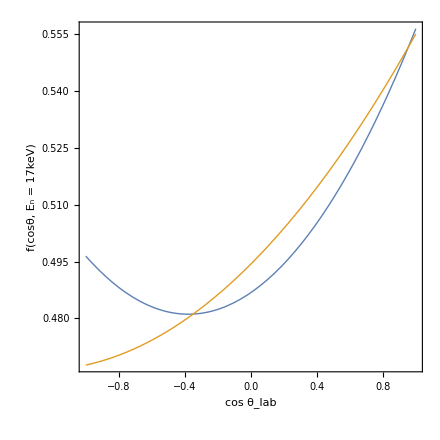

```mathematica
Plot[{f17[x,1],f17[x,2]},{x,-1,1},FrameLabel->{"cos θ_lab","f(cosθ, E_n = 17keV)"}]
```

### Differential cross section

These are approximate functions to approximate diff cross section at other energies (assumes isotropic scattering):

```mathematica
dσdErXe[Er_?NumericQ,En_?NumericQ,EM_?NumericQ]:=(xeAvgCScm2[En 10^9] Centimeter^2)/ErMax[En,EM,mn,MtXe] UnitStep[(ErMax[En,EM,mn,124amu]-Er)]
```

```mathematica
dσdErAr[Er_?NumericQ,En_?NumericQ,EM_?NumericQ]:=(arCS[En 10^9] 10^-24 Centimeter^2)/ErMax[En,EM,mn,MtAr] UnitStep[(ErMax[En,EM,mn,MtAr]-Er)]
```

Define interpolated E_n = 17 keV differential cross section:

```mathematica
dσi17dErXE[Er_?NumericQ,EMGeV_?NumericQ,ii_?NumericQ]:= If[(ErMax[17 10^-6,EMGeV,mn,isotopesA[[ii]]amu]>Er )&&(Er>ErMin[17 10^-6,EMGeV,mn,isotopesA[[ii]]amu])
,
Return[(xeCS[[ii]][17 10^3] 10^-24 Centimeter^2)f17[cosθi[Er,17 10^-6,EMGeV,mn,isotopesA[[ii]]amu],ii](-dcosθdEr[Er,17 10^-6 ,EMGeV,mn,isotopesA[[ii]]amu])];
,
Return[0];
];
```

```mathematica
dσ17dErAR[Er_?NumericQ,EMGeV_?NumericQ]:= If[(ErMax[17 10^-6,EMGeV,mn,MtAr]>Er )&&(Er>ErMin[17 10^-6,EMGeV,mn,MtAr])
,
Return[(arCS[17 10^3] 10^-24 Centimeter^2)f17ar[cosθi[Er,17 10^-6,EMGeV,mn,MtAr]](-dcosθdEr[Er,17 10^-6 ,EMGeV,mn,MtAr])];
,
Return[0];
];
```

Check that the modified kinematics preserve the normalization of the total cross section:

```mathematica
Sum[isoFrac[[ii]]NIntegrate[dσi17dErXE[Er,0,ii],{Er,0,ERmax[17 keV,mn,isotopesA⟦ii⟧ amu]}],{ii,Length[isotopesA]}]
```

18618.2

Indeed it matches:

```mathematica
xeAvgCScm2[(17keV)/eV] Centimeter^2
```

18610.6

Also matches for argon:

```mathematica
{NIntegrate[dσ17dErAR[Er,0],{Er,0,ERmax[17 10^-6,mn,MtAr]}],(arCS[(17keV)/eV] 10^-24 Centimeter^2)}
```

{1010.85,1010.87}

## Elastic nuclear recoil rate

The differential rate per unit detector mass is:
dR/dE_R = 1/m_T ϕ_ndσ/dE_R

Here we average it over the isotopes:

```mathematica
dR17dErXE[Er_?NumericQ,EM_?NumericQ,ϕ_?NumericQ]:= ϕ/MtXe Sum[isoFrac[[ii]]dσi17dErXE[Er,EM,ii],{ii,Length[isotopesXe]}]
```

```mathematica
dR17dErAR[Er_?NumericQ,EM_?NumericQ,ϕ_?NumericQ]:= ϕ 1/MtAr dσ17dErAR[Er,EM]
```

Approximate rates for other energies (assuming isotropy):

```mathematica
dRdErXe[Er_?NumericQ,EM_?NumericQ,EN_?NumericQ,ϕ_?NumericQ]:= ϕ 1/MtXe dσdErXe[Er,EN,EM];
dRdErAr[Er_?NumericQ,EM_?NumericQ,EN_?NumericQ,ϕ_?NumericQ]:= ϕ 1/MtAr dσdErAr[Er,EN,EM];
```

Compare interpolated rate:

```mathematica
rateUnits=(Kilogram/(1(*kg*))Second/(1(*s*))(10^-6(*GeV*))/(1(*keV*)));
```

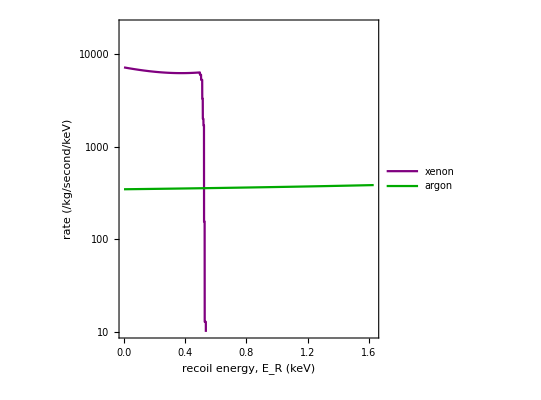

```mathematica
LogPlot[{dR17dErXE[Er keV,0,Φreactor]rateUnits,dR17dErAR[Er keV,0,Φreactor]rateUnits},{Er,0,ERmax[17 10^-6,mn,MtAr]/keV},
PlotRange->{10,2 10^4},PlotStyle->{Purple,Darker[Green]},
PlotLegends->Legend[{"xenon","argon"}],FrameLabel->{"recoil energy, E_R (keV)","rate (/kg/second/keV)"}]
```

Total rate assuming volume equally “illuminated” by average flux of neutrons:

```mathematica
totalRawNRrate=NIntegrate[dR17dErXE[Er,0,Φreactor],{Er,0,ERmax[17 10^-6,mn,124amu]},PrecisionGoal->4]events Kilogram/(1kg)Second/(1s)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(3318.87 events)/(kg s)

```mathematica
totalRawNRrate=NIntegrate[dR17dErAR[Er,0,Φreactor],{Er,0,ERmax[17 10^-6,mn,MtAr]},PrecisionGoal->4]events Kilogram/(1kg)Second/(1s)
```

(592.598 events)/(kg s)

Export tabulated rate for thinNEST calculation:

```mathematica
neutronRateDat = Table[{Er, dR17dEr[Er*keV, 0, 1]}, {Er, 0.001, ERmax[17keV, mn, 128*amu]/keV, 0.001}]; 
Export["neutron_NR_xe.dat", neutronRateDat];
```

## Migdal rate

### Import

```mathematica
datXe=Import["data/Xe_new.dat"];
datSepXe=Table[datXe[[4+254j;;254+254j]],{j,0,Floor[Length[datXe]/256]}];
```

```mathematica
datAr=Import["data/Ar.dat"];
datSepAr=Table[datAr[[4+254j;;254+254j]],{j,0,Floor[Length[datAr]/256]}];
```

#### Reproducing Fig.3 of Ibe et al.

Xenon

```mathematica
datN1=Table[datXe[[4+254j;;254+254j]],{j,0,0}];
datN2=Table[datXe[[4+254j;;254+254j]],{j,1,2}];
datN3=Table[datXe[[4+254j;;254+254j]],{j,3,5}];
datN4=Table[datXe[[4+254j;;254+254j]],{j,6,8}];
datN5=Table[datXe[[4+254j;;254+254j]],{j,9,10}];
```

```mathematica
totN1={datN1[[1,All,1]]/1000,1000/(2π)((10^-3 me)/(10^-9(*1eV*)))^2 datN1[[All,All,2]][[1]]}//Thread;
totN2={datN2[[1,All,1]]/1000,1000/(2π)((10^-3 me)/(10^-9(*1eV*)))^2 Apply[Plus,datN2[[All,All,2]]]}//Thread;
totN3={datN3[[1,All,1]]/1000,1000/(2π)((10^-3 me)/(10^-9(*1eV*)))^2 Apply[Plus,datN3[[All,All,2]]]}//Thread;
totN4={datN4[[1,All,1]]/1000,1000/(2π)((10^-3 me)/(10^-9(*1eV*)))^2 Apply[Plus,datN4[[All,All,2]]]}//Thread;
totN5={datN5[[1,All,1]]/1000,1000/(2π)((10^-3 me)/(10^-9(*1eV*)))^2 Apply[Plus,datN5[[All,All,2]]]}//Thread;
```

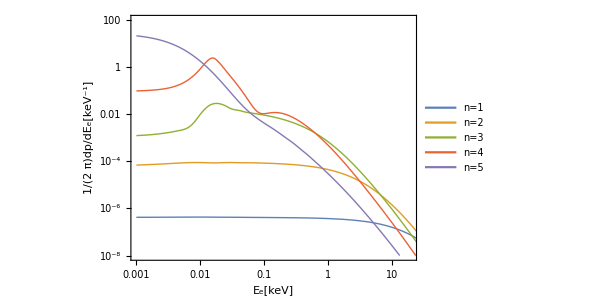

```mathematica
plot=ListLogLogPlot[{totN1,totN2,totN3,totN4,totN5},Joined->True,AspectRatio->.7,PlotRange->{{.001,20},{10^-8,100}},PlotLegends->Legend[{"n=1","n=2","n=3","n=4","n=5"}],FrameLabel->{"E_e[keV]","1/(2  π)dp/dE_e[keV^-1]"},FrameTicks->{LogTicks[10^-8,100,2],LogTicks[.001,10]}]
```

### Migdal definitions

Momentum transfer to electron:

```mathematica
qe[Er_,mT_]=me √((2Er)/mT);
```

List of states contained in the file

```mathematica
statesXe=Table[datXe[[2+254j]],{j,0,Floor[Length[datXe]/256]}];
statesAr=Table[datAr[[2+254j]],{j,0,Floor[Length[datAr]/256]}];
```

List of binding energies of the states in GeV

```mathematica
EstatesXe=eV{3.5 10^4,5.4 10^3,4.9 10^3,1.1 10^3,9.3 10^2,6.6 10^2,2.0 10^2,1.4 10^2,6.1 10,2.1 10,9.8};
EstatesAr=eV{3.2  10^3,3.0 10^2,2.4 10^2,2.7 10,1.3 10};
```

Array of binding energies in GeV, can be accessed as Enl[[n,l]]

```mathematica
EnlXe=eV{{3.5 10^4,0,0,0},{5.4 10^3,4.9 10^3,0,0},{1.1 10^3,9.3 10^3,6.6 10^2,0},{2.0 10^2,1.4 10^2,6.1 10,0.85},{2.1 10,9.8,1.6,0},{6.3,2.2,0,0}};
EnlAr=eV{{3.2 10^3,0,0,0},{3.2 10^2,2.4 10^2,0,0},{2.7 10,13,0,0},{0,0,0,0}};
```

Ionization probability for the n,l state into a free state with momentum qe and kinetic energy Ee, 
These were calculated at qe  = 1eV, scale probability for other momenta by (qe/(1eV))^2

```mathematica
z[x_]=0;
znlxeTable=Table[If[EnlXe[[ni,li+1]]>0,(Switch@@Join[{{ni,li}},({statesXe,Table[datSepXe[[i]]//Interpolation,{i,1,datSepXe//Length}]}//Thread//Flatten[#,1]&)]),z],{ni,1,Length[EnlXe]},{li,0,3}];
```

```mathematica
ZnlXe[n_?IntegerQ,l_?IntegerQ,qe_?NumericQ,Ee_?NumericQ]:=(qe/(10^-9(*1eV in GeV*)))^2 10^9/(2π)If[Ee<10^-9,
znlxeTable⟦n,l+1⟧[1],
If[Ee>70 10^-6,
0,
znlxeTable⟦n,l+1⟧[Ee 10^9]]
];
```

```mathematica
znlArTable=Table[If[EnlAr[[ni,li+1]]>0,(Switch@@Join[{{ni,li}},({statesAr,Table[datSepAr[[i]]//Interpolation,{i,1,datSepAr//Length}]}//Thread//Flatten[#,1]&)]),z],{ni,1,Length[EnlAr]},{li,0,3}];
```

```mathematica
ZnlAr[n_?IntegerQ,l_?IntegerQ,qe_?NumericQ,Ee_?NumericQ]:=(qe/(10^-9(*1eV in GeV*)))^2 10^9/(2π)If[Ee<10^-9,
znlArTable⟦n,l+1⟧[1],
If[Ee>70 10^-6,
0,
znlArTable⟦n,l+1⟧[Ee 10^9]]
];
```

Calc total probability at qe = 1eV

```mathematica
totMigProb=Table[NIntegrate[ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],10^-9,ee],{ee,10^-9,70 10^-6},PrecisionGoal->4],{nl,1,11}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {2.06593×10^-8}. NIntegrate obtained 1.38585×10^-7 and 5.67367×10^-11 for the integral and error estimates.

```mathematica
totMigProbXe=Table[NIntegrate[ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],10^-9,ee],{ee,10^-9,70 10^-6},PrecisionGoal->4],{nl,1,Length[EstatesXe]}];
totMigProbAr=Table[NIntegrate[ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],10^-9,ee],{ee,10^-9,70 10^-6},PrecisionGoal->4],{nl,1,Length[EstatesAr]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {2.06593×10^-8}. NIntegrate obtained 1.38585×10^-7 and 5.67367×10^-11 for the integral and error estimates.

Define function for rescaling total probability:

```mathematica
totalMigProbNL[nl_,qe_]:=(qe/10^-9)^2 totMigProb[[nl]]
```

This should match table II of Ibe et al.:

```mathematica
Table[totalMigProbNL[nl,me 10^-3],{nl,1,11}]
```

{4.8599×10^-6,0.0000296837,0.00013302,0.000110907,0.000604209,0.00357041,0.00035494,0.00146766,0.0361875,0.000468723,0.0780763}

Define some functions for the probability that will be useful in the MC:

```mathematica
migProbs=totMigProb;
```

Max probability density:

```mathematica
maxProbs=Table[datSepXe[[nl,All,2]]//Max,{nl,1,11}];
maxMigProb[nl_,qe_]:=10^9/(2π)(qe/10^-9)^2 maxProbs[[nl]]
```

Define a function that gives the probability below a given electron energy:

```mathematica
probBelowDat=ParallelTable[
Table[{EeMax,
NIntegrate[ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],10^-9,ee],
{ee,.5 10^-9,EeMax},PrecisionGoal->3]},
{EeMax,10^-9,70 10^-6,(70 10^-6)/1000}]//Interpolation[#,InterpolationOrder->1]&,{nl,1,11}];
probsBelowEe[nl_,EeMax_]:=If[EeMax<10^-9,0,probBelowDat[[nl]][EeMax]]
```

Approximate quenching factor in xenon:

```mathematica
LXe=0.15;
LAr=0.25;
```

Migdal integration limits (since we now have to integrate Er for a constant Edet:

Define integration limits:

```mathematica
(ErMIN==-(MN (-2 En mT+EM (MN+mT)+2 √(En mT (En mT-EM (MN+mT)))))/(MN+mT)^2/.EM->Edet-L ErMIN)//Solve[#,ErMIN]&//FullSimplify
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{ErMIN→(Edet MN ((-1+L) MN-mT)+2 En MN mT-2 √(En MN^2 mT (Edet (-1+L) MN-Edet mT+En mT)))/(MN-L MN+mT)^2},{ErMIN→(Edet MN ((-1+L) MN-mT)+2 (En MN mT+√(En MN^2 mT (Edet (-1+L) MN-Edet mT+En mT))))/(MN-L MN+mT)^2}}

```mathematica
ErMinMig[Edet_?NumericQ,En_?NumericQ,mT_?NumericQ,L_?NumericQ]:=(Edet mn ((-1+L) mn-mT)+2 En mn mT-2 √(En mn^2 mT (Edet (-1+L) mn-Edet mT+En mT)))/(mn-L mn+mT)^2
ErMaxMig[Edet_?NumericQ,En_?NumericQ,mT_?NumericQ,L_?NumericQ]:=(Edet mn ((-1+L) mn-mT)+2 (En mn mT+√(En mn^2 mT (Edet (-1+L) mn-Edet mT+En mT))))/(mn-L mn+mT)^2
```

These limits aren’t very different:

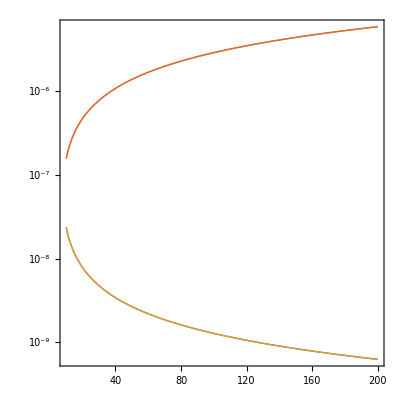

```mathematica
LogPlot[{ErMin[en keV,8keV,mn,131 amu],ErMinMig[8keV,en keV,131amu,0.15],ErMax[en keV,8keV,mn,131 amu],ErMaxMig[8keV,en keV,131amu,0.15]},{en,10,200}]
```

### Define rates

The dependent variable is now the detected energy:
  E_det=L Er+EM
Replace 
  EM = Edet - Leff Er

```mathematica
dRmigdEdetNxe[Edet_?NumericQ,Φn_?NumericQ,Ni_?IntegerQ]:= 
Φn NIntegrate[
dR17dEr[Er,Edet-LXe Er,1]*
UnitStep[EemMax[17 10^-6,mn,136amu]-Edet-LXe Er] Sum[
UnitStep[(Edet-LXe Er)-EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[Er,MtXe],(Edet-LXe Er)-EstatesXe[[nl]]],
{nl,Flatten[Position[statesXe[[All,1]],Ni]]}],
{Er,ErMin[17 10^-6,Edet,mn,136 amu],ErMax[17 10^-6,Edet,mn,124 amu]},
PrecisionGoal->3]
```

```mathematica
dRmigdEdetNar[Edet_?NumericQ,Φn_?NumericQ,Ni_?IntegerQ]:= 
Φn NIntegrate[
dR17dErAR[Er,Edet-LAr Er,1]*
UnitStep[EemMax[17 10^-6,mn,40amu]-Edet-LAr Er] Sum[
UnitStep[(Edet-LAr Er)-EstatesAr[[nl]]]*
ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],qe[Er,MtAr],(Edet-LAr Er)-EstatesAr[[nl]]],
{nl,Flatten[Position[statesAr[[All,1]],Ni]]}],
{Er,ErMin[17 10^-6,Edet,mn,MtAr],ErMax[17 10^-6,Edet,mn,MtAr]},
PrecisionGoal->3]
```

### Rate plots

#### Calculate rate

```mathematica
dataEM3iXE=ParallelTable[{Em/keV,dRmigdEdetNxe[Em ,Φreactor,3]rateUnits},{Em,logSpace[EnlXe[[3,3]],8keV,200]}];
dataEM4iXE=ParallelTable[{Em/keV,dRmigdEdetNxe[Em ,Φreactor,4]rateUnits},{Em,logSpace[EnlXe[[4,3]],4keV,200]}];
dataEM5iXE=ParallelTable[{Em/keV,dRmigdEdetNxe[Em ,Φreactor,5]rateUnits},{Em,logSpace[EnlXe[[5,2]],2keV,200]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.62176×10^-8}. NIntegrate obtained 5.25412 and 0.00592491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {8.70694×10^-9}. NIntegrate obtained 17.5569 and 0.0252172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {1.74827×10^-8}. NIntegrate obtained 73.0107 and 0.0972505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {3.60133×10^-8}. NIntegrate obtained 345.478 and 1.32147 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.10106×10^-7}. NIntegrate obtained 191236. and 306.2 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.10272×10^-7}. NIntegrate obtained 85828.7 and 112.827 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.09977×10^-7}. NIntegrate obtained 60381.4 and 67.4568 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {3.6128×10^-9}. NIntegrate obtained 741.933 and 2.03389 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {7.41028×10^-9}. NIntegrate obtained 3119.51 and 5.60688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {9.38703×10^-9}. NIntegrate obtained 4995.28 and 7.64062 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.22034312527692×10^-7}. NIntegrate obtained 88335.7 and 152.393 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.21796258192142×10^-7}. NIntegrate obtained 59720.6 and 81.3575 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.21752915454213×10^-7}. NIntegrate obtained 42049. and 46.7037 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
dataEM1iAR=ParallelTable[{Em/keV,dRmigdEdetNar[Em,Φreactor,1]rateUnits},{Em,logSpace[EnlAr[[1,1]],7keV,200]}];
dataEM2iAR=ParallelTable[{Em/keV,dRmigdEdetNar[Em,Φreactor,2]rateUnits},{Em,logSpace[EnlAr[[2,2]],5keV,200]}];
dataEM3iAR=ParallelTable[{Em/keV,dRmigdEdetNar[Em,Φreactor,3]rateUnits},{Em,logSpace[EnlAr[[3,2]],2.1keV,200]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {1.01486×10^-7}. NIntegrate obtained 0.303155 and 0.000910983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {1.52922×10^-7}. NIntegrate obtained 0.688097 and 0.00165768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {2.04309×10^-7}. NIntegrate obtained 1.2253 and 0.00245845 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {1.47728×10^-8}. NIntegrate obtained 1.97065 and 0.00240064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {1.10614×10^-7}. NIntegrate obtained 201.943 and 0.395992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {1.264×10^-7}. NIntegrate obtained 267.692 and 0.436259 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {7.14741×10^-9}. NIntegrate obtained 237.044 and 0.876618 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {8.70975×10^-9}. NIntegrate obtained 349.341 and 1.23625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {1.19748×10^-8}. NIntegrate obtained 645.986 and 1.46087 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

#### Create plot

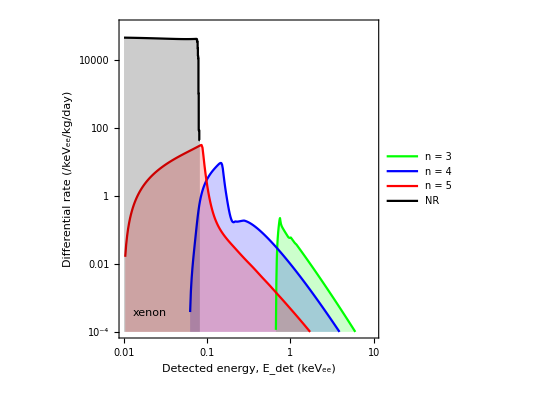
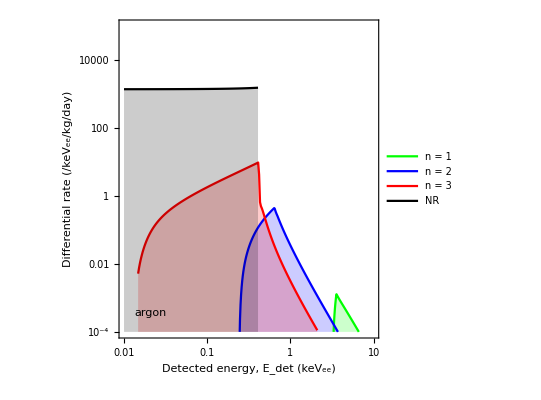

```mathematica
{migRatePlotXE=Show[ListLogLogPlot[{dataEM3iXE,dataEM4iXE,dataEM5iXE},Joined->True,
PlotRange->{{.01,10},{10^-4,10^5}},
FrameTicks->{LogTicks[10^-6,10^10,2],LogTicks[10^-3,10^1]},
FrameLabel->{"Detected energy, E_det (keV_ee)","Differential rate (/keV_ee/kg/day)"},
PlotLegends->Legend[{"n = 3","n = 4","n = 5"},Position->{.822,.775}],
PlotStyle->{Green,Blue,Red},Filling->Bottom,
Prolog->Inset[Framed[" ",FrameMargins->{{32,30},{40,40}},RoundingRadius->5,Background->White],Scaled[{.82,.81}]],
Epilog->Inset[Framed[Style["xenon",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.12,.08}]]],
LogLogPlot[
1/LXe dR17dEr[Edet /LXe 10^-6,0,Φreactor]rateUnits,
{Edet,10^-2,0.55LXe},
PlotRange->{10^-4,10^6},PlotPoints->200,
PlotStyle->Black,Filling->Bottom,
PlotLegends->Legend[{"NR"},Position->{.805,.910}]]],
migRatePlotAR=Show[ListLogLogPlot[{dataEM1iAR,dataEM2iAR,dataEM3iAR},Joined->True,
PlotRange->{{.01,10},{10^-4,10^5}},
FrameTicks->{LogTicks[10^-6,10^10,2],LogTicks[10^-3,10^1]},
FrameLabel->{"Detected energy, E_det (keV_ee)","Differential rate (/keV_ee/kg/day)"},
PlotLegends->Legend[{"n = 1","n = 2","n = 3"},Position->{.822,.775}],
PlotStyle->{Green,Blue,Red},Filling->Bottom,
Prolog->Inset[Framed[" ",FrameMargins->{{32,30},{40,40}},RoundingRadius->5,Background->White],Scaled[{.82,.81}]],
Epilog->Inset[Framed[Style["argon",18,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.12,.08}]]],
LogLogPlot[
1/LAr dR17dErAR[Edet /LAr 10^-6,0,Φreactor]rateUnits,
{Edet,10^-2,ErMax[17 10^-6,0,mn,40 amu]LAr/keV},
PlotRange->{10^-4,10^6},
PlotPoints->200,
PlotStyle->Black,Filling->Bottom,
PlotLegends->Legend[{"NR"},Position->{.805,.910}]]]}
```

```mathematica
Export["figures/fig_xe_neutron_rates.pdf",migRatePlotXE];
Export["figures/fig_ar_neutron_rates.pdf",migRatePlotAR];
```

### Integrated rate

#### Define rates

```mathematica
migRate17TotXE[EdetMin_?NumericQ,EdetMax_?NumericQ,Φn_?NumericQ]:= 
Φn NIntegrate[
dR17dErXE[Er,Edet-LXe Er,1]*
UnitStep[EemMax[17 10^-6,mn,136amu]-Edet-LXe Er] Sum[
UnitStep[(Edet-LXe Er)-EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[Er,MtXe],(Edet-LXe Er)-EstatesXe[[nl]]],
{nl,1,Length[statesXe]}],
{Edet,EdetMin,EdetMax},
{Er,ErMin[17 10^-6,Edet,mn,136amu],ErMax[17 10^-6,Edet,mn,124 amu]},
PrecisionGoal->3,Method->{"GlobalAdaptive","SymbolicProcessing"->.01}]
```

```mathematica
migRate17TotAR[EdetMin_?NumericQ,EdetMax_?NumericQ,Φn_?NumericQ]:= 
Φn NIntegrate[
dR17dErAR[Er,Edet-LAr Er,1]*
UnitStep[EemMax[17 10^-6,mn,40amu]-Edet-LAr Er] Sum[
UnitStep[(Edet-LAr Er)-EstatesAr[[nl]]]*
ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],qe[Er,MtAr],(Edet-LAr Er)-EstatesAr[[nl]]],
{nl,1,Length[statesAr]}],
{Edet,EdetMin,EdetMax},
{Er,ErMin[17 10^-6,Edet,mn,MtAr],ErMax[17 10^-6,Edet,mn,MtAr]},
PrecisionGoal->3,Method->{"LocalAdaptive","SymbolicProcessing"->.01}]
```

This alternative total rate skips going through E_det, so should be faster and more accurate than using above with full kinematic range, but makes it impossible to choose a detected energy threshold:

```mathematica
totMigRateXE[En_?NumericQ,Φn_?NumericQ]:=
Φn NIntegrate[
dRdErXe[Er,EM,En,1]*
 Sum[
UnitStep[EM-EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[Er,MtXe],EM-EstatesXe[[nl]]],
{nl,1,Length[statesXe]}],
{EM,Min[EstatesXe],EemMax[En,mn,136amu]},
{Er,ErMin[En,EM,mn,136 amu],ErMax[En,EM,mn,128 amu]},
PrecisionGoal->3]

totMigRateAR[En_?NumericQ,Φn_?NumericQ]:=
Φn NIntegrate[
dRdErAr[Er,EM,En,1]*
 Sum[
UnitStep[EM-EstatesAr[[nl]]]*
ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],qe[Er,MtAr],EM-EstatesAr[[nl]]],
{nl,1,Length[statesAr]}],
{EM,Min[EstatesAr],EemMax[En,mn,MtAr]},
{Er,ErMin[En,EM,mn,MtAr],ErMax[En,EM,mn,MtAr]},
PrecisionGoal->3]
```

It would also be interesting to know the total Migdal rate as a function of the neutron energy, this is only approximate:

```mathematica
Integrate[f[EEM,Er]DiracDelta[Edet-EEM-L Er],{Edet,Eth,Emax}]//FullSimplify
```

ConditionalExpression[f[EEM,Er] (-1+2 HeavisideTheta[Emax-Eth]) HeavisideTheta[EEM+Er L-Eth HeavisideTheta[Emax-Eth]-Emax HeavisideTheta[-Emax+Eth]] HeavisideTheta[-EEM-Er L+Emax HeavisideTheta[Emax-Eth]+Eth HeavisideTheta[-Emax+Eth]], Emax∈ℝ&&Eth∈ℝ&&Im[EEM]+Im[L] Re[Er]+Im[Er] Re[L]==0]

```mathematica
totMigRateThXe[Eth_?NumericQ,En_?NumericQ,Φn_?NumericQ]:=
Φn NIntegrate[(-1+2 UnitStep[10keV-Eth]) UnitStep[EM+Er LXe-Eth UnitStep[10keV-Eth]-10keV UnitStep[-10keV+Eth]] UnitStep[-EM-Er LXe+10keV UnitStep[10keV-Eth]+Eth UnitStep[-10keV+Eth]]
dRdErXe[Er,EM,En,1]*
 Sum[
UnitStep[EM-EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[Er,131 amu],EM-EstatesXe[[nl]]],
{nl,1,Length[statesXe]}],
{EM,.01keV,Max[EemMax[En,mn,128amu],.01keV]},
{Er,ErMin[En,EM,mn,131 amu],ErMax[En,EM,mn,128 amu]},
PrecisionGoal->3]

totMigRateThAr[Eth_?NumericQ,En_?NumericQ,Φn_?NumericQ]:=
Φn NIntegrate[(-1+2 UnitStep[25keV-Eth]) UnitStep[EM+Er LAr-Eth UnitStep[25keV-Eth]-25keV UnitStep[-25keV+Eth]] UnitStep[-EM-Er LAr+25keV UnitStep[25keV-Eth]+Eth UnitStep[-25keV+Eth]]
dRdErAr[Er,EM,En,1]*
UnitStep[EemMax[En,mn,MtAr]-EM] Sum[
UnitStep[EM-EstatesAr[[nl]]]*
ZnlAr[statesAr[[nl,1]],statesAr[[nl,2]],qe[Er,MtAr],EM-EstatesAr[[nl]]],
{nl,1,Length[statesAr]}],
{EM,.013keV,Max[EemMax[En,mn,MtAr],.013keV]},
{Er,ErMin[En,EM,mn,MtAr],ErMax[En,EM,mn,MtAr]},
PrecisionGoal->3]
```

#### Calculations

Total Migdal rate:

```mathematica
totElasticRateXE=NIntegrate[dR17dErXE[Er,0,Φreactor],{Er,0,ERmax[17 10^-6,mn,124 amu]},PrecisionGoal->3]events Kilogram/(1kg)Second/(1s)
```

(3311.41 events)/(kg s)

```mathematica
totMigdalRateXE=migRate17TotXE[.01keV,6keV,Φreactor]events Kilogram/(1kg)Second/(1s)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0887052 and 0.000144391 for the integral and error estimates.

(1.93776 events)/(kg s)

```mathematica
totElasticRateXE
```

```mathematica
totElasticRateXE/totMigdalRateXE
```

1708.88

```mathematica
1/1708.88
```

0.000585179

Therefore there is 1 Migdal event for every ~10^3 elastic scatters.

#### Total rate as function of neutron energy

Calc Migdal rates for three different threshold scenarios:

```mathematica
totMigdalRateDatXe=ParallelTable[{En/keV,totMigRateXE[En,Φreactor] Kilogram Second},{En,logSpace[1keV, 10^3 keV,400]}];
totMigdalRateDatAr=ParallelTable[{En/keV,totMigRateAR[En,Φreactor] Kilogram Second},{En,logSpace[1 keV,10^3 keV,400]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
totMigdalRateLowThDatXe=ParallelTable[{En/keV,totMigRateThXe[1keV LXe,En,Φreactor] Kilogram Second},{En,logSpace[1keV,10^3 keV,200]}];
totMigdalRateLowThDatAr=ParallelTable[{En/keV,totMigRateThAr[10keV LAr,En,Φreactor] Kilogram Second},{En,logSpace[1keV,10^3 keV,200]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in EM near {EM,Er} = {0.0582838,0.922062}. NIntegrate obtained 3.01246×10^-6 and 3.1981×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
totMigdalRateHighThDatXe=ParallelTable[{En/keV,totMigRateThXe[5keV LXe,En,Φreactor] Kilogram Second},{En,logSpace[1keV,10^3 keV,200]}];
totMigdalRateHighThDatAr=ParallelTable[{En/keV,totMigRateThAr[20keV LAr,En,Φreactor] Kilogram Second},{En,logSpace[1keV,10^3 keV,200]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in EM near {EM,Er} = {0.0253333,0.922062}. NIntegrate obtained 0.00156526 and 1.60787×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in EM near {EM,Er} = {0.0346236,0.961031}. NIntegrate obtained 0.00300244 and 3.10731×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in EM near {EM,Er} = {0.0236334,0.922062}. NIntegrate obtained 0.00138992 and 2.15637×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in EM near {EM,Er} = {0.0212962,0.922062}. NIntegrate obtained 0.000798888 and 1.37631×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in EM near {EM,Er} = {0.0262282,0.922062}. NIntegrate obtained 0.00167454 and 1.98319×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Calculate NR rates for three different threshold scenarios:

```mathematica
totNRrateDatXe=Table[{En/keV,1/MtXe xeAvgCScm2[En/eV] Centimeter^2 Φreactor Kilogram Second},{En,logSpace[1keV,10^4 keV,1000]}];
totNRrateDatAr=Table[{En/keV,1/MtAr arCS[En/eV] 10^-24 Centimeter^2 Φreactor Kilogram Second},{En,logSpace[1keV,10^4 keV,10000]}];
```

```mathematica
totNRrateLowThDatXe=ParallelTable[{EN/keV,Kilogram Second NIntegrate[dRdErXe[Er,0,EN,Φreactor],{Er,1keV,Max[1keV,ERmax[EN,mn,124 amu]]},PrecisionGoal->3] },
{EN,logSpace[20keV,10^3 keV,1000]}];
totNRrateLowThDatAr=ParallelTable[{EN/keV,Kilogram Second NIntegrate[dRdErAr[Er,0,EN,Φreactor],{Er,10keV,Max[10keV,ERmax[EN,mn,MtAr]]},PrecisionGoal->3] },
{EN,logSpace[20keV,10^3 keV,1000]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
totNRrateHighThDatXe=ParallelTable[{EN/keV,Kilogram Second NIntegrate[dRdErXe[Er,0,EN,Φreactor],{Er,5keV,Max[5keV,ERmax[EN,mn,124 amu]]},PrecisionGoal->3] },
{EN,logSpace[20keV,10^3 keV,1000]}];
totNRrateHighThDatAr=ParallelTable[{EN/keV,Kilogram Second NIntegrate[dRdErAr[Er,0,EN,Φreactor],{Er,20keV,Max[20keV,ERmax[EN,mn,MtAr]]},PrecisionGoal->3] },
{EN,logSpace[20keV,10^3 keV,1000]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Neutron capture rates (all above threshold):

```mathematica
totNCrateDatXe=Table[{En/keV,1/MtXe xeAvgNCCScm2[En/eV] Centimeter^2 Φreactor Kilogram Second},{En,logSpace[1keV,10^4 keV,1000]}];
totNCrateDatAr=Table[{En/keV,1/MtAr arNCCScm2[En/eV] Centimeter^2 Φreactor Kilogram Second},{En,logSpace[1keV,10^4 keV,10000]}];
```

InterpolatingFunction::dmval: Input value {1.25173×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.25288×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.25404×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Plot the result for xenon:

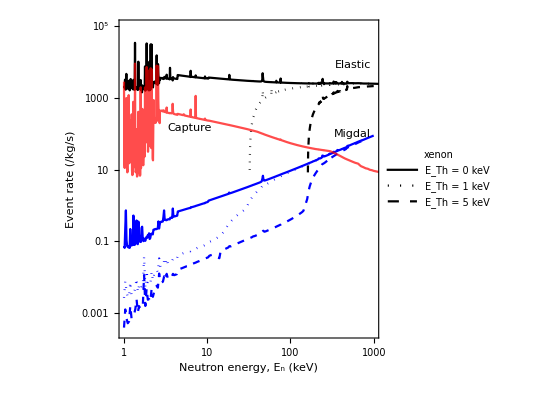

```mathematica
ratePlotXe=ListLogLogPlot[{totNRrateDatXe,totNRrateLowThDatXe,totNRrateHighThDatXe,totMigdalRateDatXe,totMigdalRateLowThDatXe,totMigdalRateHighThDatXe,totNCrateDatXe},Joined->True,ImageSize->400,
PlotRange->{{1,10^3},{3 10^-4,10^5}},
FrameTicks->{LogTicks[10^-6,10^10,2],LogTicks[10^0,10^10]},
FrameLabel->{"Neutron energy, E_n (keV)","Event rate (/kg/s)"},
PlotLegends->Legend[{"E_Th = 0 keV","E_Th = 1 keV","E_Th = 5 keV"},Position->{.8,.18},LegendMarkerSize->{20,10},LegendMargins->2,LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&),LegendLabel->Style["xenon",16,FontFamily->"Times"]],
PlotStyle->{Black,{Black,Dotted},{Black,Dashed},Blue,{Blue,Dotted},{Blue,Dashed},{Opacity[.7,Red]}},
GridLines->{{17,24,47,59,82},None},
Epilog->{(*Style[Text["17 keV",Scaled[{.29,.1}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],Style[Text["24 keV",Scaled[{.37,.1}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],Style[Text["47 keV",Scaled[{.46,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["59 keV",Scaled[{.72,.2}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],
Style[Text["82 keV",Scaled[{.51,.1}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],*)
Style[Text["Capture",Scaled[{.27,.66}],Automatic,{1,-.15}],16,FontFamily->"Times",Opacity[.7,Red]],
Style[Text["Migdal",Scaled[{.9,.64}],Automatic,{1.6,.56}],16,FontFamily->"Times",Blue],
Style[Text["Elastic",Scaled[{.9,.86}],Automatic,{1,0}],16,FontFamily->"Times",Black]}]
```

Plot result for argon:

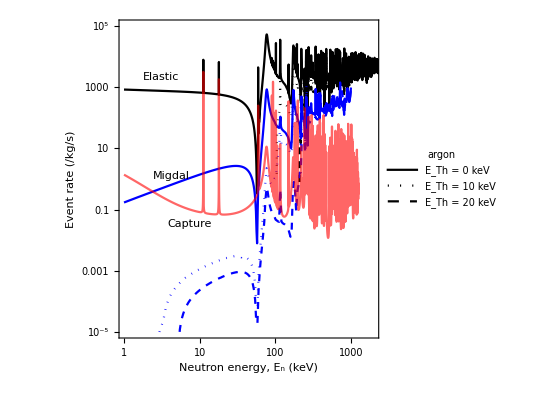

```mathematica
ratePlotAr=ListLogLogPlot[{totNRrateDatAr,totNRrateLowThDatAr,totNRrateHighThDatAr,totMigdalRateDatAr,totMigdalRateLowThDatAr,totMigdalRateHighThDatAr,totNCrateDatAr},Joined->True,ImageSize->400,
PlotRange->{{1,2 10^3},{10^-5,10^5}},
FrameTicks->{LogTicks[10^-6,10^10,2],LogTicks[10^0,10^10]},
FrameLabel->{"Neutron energy, E_n (keV)","Event rate (/kg/s)"},
PlotLegends->Legend[{"E_Th = 0 keV","E_Th = 10 keV","E_Th = 20 keV"},Position->{.8,.18},LegendMarkerSize->{20,10},LegendMargins->2,LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&),LegendLabel->Style["argon",16,FontFamily->"Times"]],
PlotStyle->{Black,{Black,Dotted},{Black,Dashed},Blue,{Blue,Dotted},{Blue,Dashed},{Opacity[.6,Red]}},
GridLines->{{17,24,47,59,82},None},
Epilog->{(*Style[Text["17 keV",Scaled[{.29,.35}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],Style[Text["24 keV",Scaled[{.37,.3}],Automatic,{0,1}],16,FontFamily->"Times",LineSpacing->1.5],*)
Style[Text["Capture",Scaled[{.27,.36}],Automatic,{1,-.15}],16,FontFamily->"Times",Opacity[.7,Red]],
Style[Text["Elastic",Scaled[{.16,.82}],Automatic,{1,0}],16,FontFamily->"Times"],Style[Text["Migdal",Scaled[{.2,.51}],Automatic,{1.4,.4}],16,FontFamily->"Times",Blue]
}]
```

```mathematica
Export["figures/fig_xe_neutronEn_rate.pdf",ratePlotXe];
Export["figures/fig_ar_neutronEn_rate.pdf",ratePlotAr];
```

## Test MC implementation

### Energy spectrum

Create an inverse CDF of the rate to sample NR energies from (expect this code to ~2 mins to run):

```mathematica
norm=NIntegrate[dR17dEr[Er,0,1],{Er,0.,ERmax[17 10^-6,mn,128 amu]},MinRecursion->4];
neutronRateInvCDFdat=ParallelTable[{NIntegrate[dR17dEr[Er,0,1]/norm,{Er,0,ERup},PrecisionGoal->4],ERup 10^6},{ERup,0,ERmax[17 10^-6,mn,128 amu],ERmax[17 10^-6,mn,128 amu]/4000}];
neutronRateInvCDF=Interpolation[neutronRateInvCDFdat,InterpolationOrder->1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.11098×10^-7}. NIntegrate obtained 152.032 and 0.00160774 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.10723594756976×10^-7}. NIntegrate obtained 0.997418 and 0.000103732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.10833118572158×10^-7}. NIntegrate obtained 0.998263 and 0.000103016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {5.1058521255546496041032697899182679623919511868734844028949737549×10^-7}. NIntegrate obtained 0.9999 and 0.00012148 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Create inverse CDF for each Znl function:

```mathematica
znlRateInvCDFdat=ParallelTable[{NIntegrate[ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],10^-9,ee]/totMigProb⟦nl⟧,{ee,10^-9,Eeup},PrecisionGoal->4],Eeup},{nl,1,11},{Eeup,10^-9,70 10^-6,(70 10^-6)/2000}];
ZnlInvCDF=Interpolation[#,InterpolationOrder->1]&/@znlRateInvCDFdat;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {2.3041×10^-8}. NIntegrate obtained 0.99998 and 0.00611202 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {2.31491×10^-8}. NIntegrate obtained 0.999944 and 0.0059429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {2.32571×10^-8}. NIntegrate obtained 0.999906 and 0.00573207 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {2.54007×10^-8}. NIntegrate obtained 0.999997 and 0.000100546 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {2.54293×10^-8}. NIntegrate obtained 0.999997 and 0.00010166 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {2.56003×10^-8}. NIntegrate obtained 0.999998 and 0.000105715 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Generate 200k points with probabilities scaled for better sampling efficiency:

This should take approximately 8 hours to run with 8 cores.

```mathematica
totalMigProb[ENR_,mT_]:=(qe[ENR,mT]/10^-9)^2 Sum[probsBelowEe[nl,EemMaxER[ENR,17 10^-6,mn,mT]-EstatesXe⟦nl⟧],{nl,1,11}]
```

```mathematica
maxTotCumulativeProb=NMaximize[{totalMigProb[enr,128mn],enr>0,enr<.52 10^-6},enr][[1]];
```

```mathematica
(*Use scaled probabilties to improve sampling efficiency*)
{time,MCdata}=ParallelTable[
Block[{ERNRkeV,ERERkeV,EMmax,EeMax,Ee,nl,cumulativeProb,r,mTi,nn},
ERERkeV=-1;
While[ERERkeV<0,

(*Get a random nuclear recoil energy from neutron spectrum*)
ERNRkeV=neutronRateInvCDF[RandomReal[]];

(*choose a random isotope to scatter from (technically there should be a diff function for each isotope)*)
mTi=RandomChoice[isoFrac->isotopesA,1][[1]]amu;

(*calculate the maximum electromagnetic energy kinematically available*)
EMmax=EemMaxER[ERNRkeV 10^-6,17 10^-6,mn,mTi];

(*make a list of cumulative scaled total probabilities up to EMmax=Ee+Enl*)
cumulativeProb=(qe[ERNRkeV 10^-6,mTi]/10^-9)^2 Table[probsBelowEe[nli,EMmax-EstatesXe[[nli]]],{nli,1,11}];
(*cumulativeProb=(qe[ERNRkeV 10^-6,mTi]/10^-9)^2 Table[Sum[probsBelowEe[ii,EMmax-EstatesXe[[ii]]],{ii,1,nli}],{nli,1,11}];*)
totCumulativeProb=cumulativeProb;
Do[totCumulativeProb[[ii]]+=totCumulativeProb[[ii-1]],{ii,2,11}];
If[totCumulativeProb[[-1]]>0,
totCumulativeProb/=maxTotCumulativeProb;
(*get a random number (0-1) to test against probability of ionization from each shell*)
(*loop over shells, break when successful*)
r=RandomReal[];
nl=1;
While[nl<12,
If[r<totCumulativeProb[[nl]],Break[]];
nl++;
];
(*randomly select energy of ejected electron*)
If[nl<12,
EeMax=EMmax -EstatesXe[[nl]];
Ee=ZnlInvCDF⟦nl⟧[RandomReal[]];nn=1;
While[Ee>EeMax,
Ee=ZnlInvCDF⟦nl⟧[RandomReal[]];
ERERkeV=(Ee+EstatesXe[[nl]])10^6;nn++;
];
(*Ee=(EMmax -EstatesXe[[nl]])*RandomReal[];nn=1;
While[RandomReal[]maxMigProb[nl,qe[ERNRkeV 10^-6,mTi]]>ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qe[ERNRkeV 10^-6,mTi],Ee],
Ee=(EMmax -EstatesXe[[nl]])*RandomReal[];
ERERkeV=(Ee+EstatesXe[[nl]])10^6;nn++;
]*);
];
];
];
{ERNRkeV,ERERkeV,nn}]
,500,Method->"FinestGrained"]//AbsoluteTiming;
```

```mathematica
NotebookDirectory[]//SetDirectory;
MCdata=Import["results/migdal_mc_dat_op.dat"];
```

```mathematica
Export["results/migdal_mc_dat.dat",MCdata];
```

Import pre-calculated MC data

```mathematica
MCdata0=Import["results/migdal_mc_dat.dat","Table"];
```

Calculate number of events expected in each bin numerically:

```mathematica
norm=migRateTot[.0098 10^-6,EemMax[17 10^-6,mn,128amu],1]/Length[MCdata];migRateBinned=ParallelTable[{ErM 10^6+.025,migRateTot[ErM,ErM+.05 10^-6,1]/norm},{ErM,0.0,3 10^-6,.05 10^-6}];
```

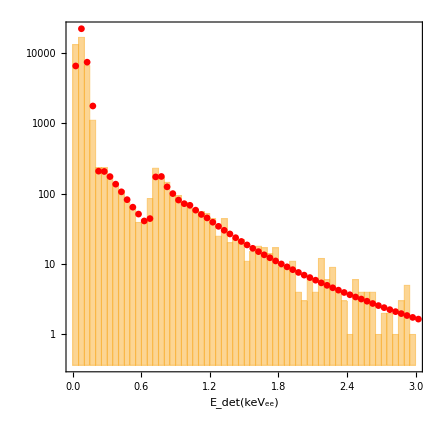

```mathematica
Show[
Histogram[{.15 MCdata[[All,1]]+MCdata[[All,2]]},
{0,3,.05},{"Log","Count"},
FrameLabel->{"E_det(keV_ee)"}],
ListLogPlot[migRateBinned,PlotStyle->Red]]
```

### Random location

#### Along path

This will be implemented in the Monte-Carlo using NEST

```mathematica
dPldx[x_,ll_]=1/ll Exp[-x/ll]
```

ⅇ^(-x/ll)/ll

The invCDF:

```mathematica
p==Integrate[dPldx[x,ll],{x,0,X}]//Solve[#,X]&
```

{{X→ConditionalExpression[ll (2 ⅈ π C[1]+Log[1/(1-p)]),C[1]∈ℤ]}}

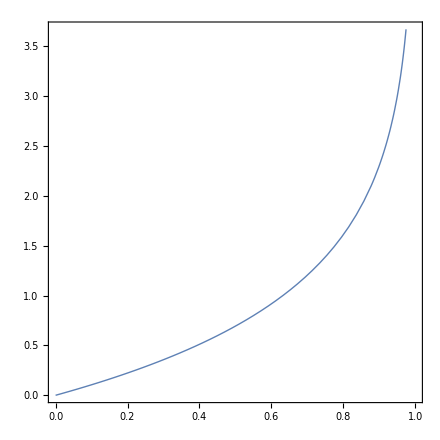

```mathematica
Plot[Log[1/(1-p)],{p,0,1}]
```

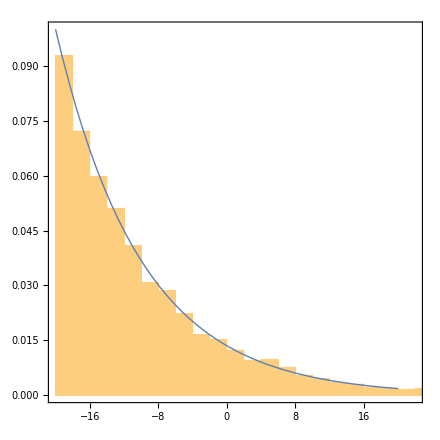

```mathematica
Table[10Log[1/(1-RandomReal[])]-20,10000]//Show[Histogram[#,Automatic,"PDF"],Plot[dPldx[x+20,10],{x,-20,20}]]&
```

#### Perpendicular to path

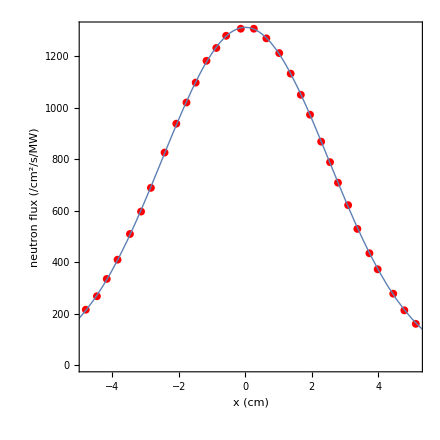

```mathematica
Show[ListPlot[beamDat,PlotStyle->Red,
FrameLabel->{"x (cm)","neutron flux (/cm^2/s/MW)"}],
Plot[a Exp[-(r-μi)^2/(2 σ^2)]/.beamFit,{r,-6,6}]]
```

```mathematica
250/Centimeter^2/Second
```

Create random samples in 2D:

```mathematica
randBeamDat=RandomVariate[NormalDistribution[μi,σ]/.beamFit,{100000,2}];
```

```mathematica
randBeamDat//Histogram3D
```

-Graphics3D-

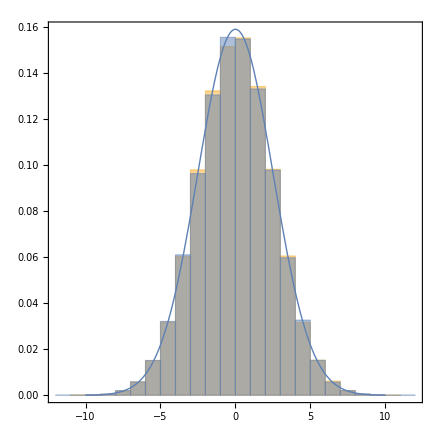

```mathematica
Show[Histogram[{randBeamDat[[All,1]],randBeamDat[[All,2]]},Automatic,"Probability"],Plot[PDF[NormalDistribution[μi,σ],x]/.beamFit,{x,-10,10}]]
```

## S1S2 distribution

The above algorithm is also implemented in thinNEST, which uses NEST to perform a MC and detector simulation.

### Detector geometry

Density of xenon @ 173K:

```mathematica
ρXe=2.8611g/cm^3;
```

We imagine a detector with a r = 10cm, z = 12cm fiducial region:

```mathematica
rDet=10cm;
zDet=12cm;
fidMass=(π rDet^2 zDet)ρXe((1kg)/(10^3 g))
```

10.7861 kg

-Graphics-

Some dimensions:

```mathematica
cathZ=20mm; 
dt0=195mm;
anodeZ=200mm;
fidBotZ=cathZ+20mm;
fidTopZ=fidBotZ+120mm;
```

The drift velocity @100V(taken from NEST):

```mathematica
vD100=1.33748mm/μs;
```

```mathematica
dtMin=(dt0-fidTopZ)/vD100
```

26.1686 μs

```mathematica
dtMax=(dt0-fidBotZ)/vD100
```

115.89 μs

```mathematica
dtCntr=dt0/2/vD100
```

72.8983 μs

### Define plot function

```mathematica
CredibleGridPlot2D//Clear;
CredibleGridPlot2D[data_, range_,opt:OptionsPattern[{CredibleLevel -> {0.6827,0.9545}, LoggedData->{False,False}, FrameTicks->False, Smoothing->False, MaxPoint->False, SimPoint->{∞,∞}, ShowDensity->False, CredibleColor->Blue, ListContourPlot}]] := 
Module[{binData,cl, p, minx, miny, maxx, maxy, xbin, ybin, xNbins, yNbins, ft, ftX, ftY, contourPlot, densityPlot, dr, pr, prX, prY, maxPoint, maxPointCross, contSty}, 
	binData=data/Plus@@Flatten[data];
	If[Dimensions[binData]≠2,Return["List data does not have suitable dimensions"];];
	xNbins = Length[binData];
  yNbins=Length[binData[[1]]];

  minx = range[[1,1]]; 
	maxx =range[[1,2]]; 
	miny = range[[2,1]]; 
	maxy = range[[2,2]]; 
	xbin = (maxx - minx)/xNbins; 
	ybin = (maxy - miny)/yNbins; 

	(*binData = ((BinLists[ data, {minx, maxx, xbin}, {miny, maxy, ybin}, {0, 1, 1}][[All, All, 1]] // Apply[Plus, #, {2}] & ) /. 0 -> {0, 0, 0})[[All, All, 3]]//Transpose;*)

	If[OptionValue[Smoothing]==True, 
	    binData = (ArrayPad[#1, 1, 0] & )[ImageData[(GaussianFilter[#1, {2, 2}] & )[Image[binData]]]];
	    dr = {{minx - (3*xbin)/2, maxx + (3*xbin)/2}, {miny - (3*ybin)/2, maxy + (3*ybin)/2}};
	    ,
              dr = {{minx, maxx}, {miny, maxy}};
	  ];
    
    pr=FilterRules[{opt}, PlotRange];   

    If[pr == {},
        pr = {{minx,maxx},{miny,maxy},All};
        ,
        If[Length[pr[[1,2]]]==0,
         pr = {{minx,maxx},{miny,maxy},All};
        ];
        If[Depth[pr[[1,2]]]==2,
         pr=Join[{{minx,maxx}},{pr[[1,2]]},{All}]
        ];
        If[Length[pr[[1,2]]]==3,
         pr=pr[[1,2]];
        ,
            If[Length[pr[[1,2]]]==2,
             pr=Join[pr[[1,2]],{All}]
            ];
        ];
        
      ];
      
   ft = OptionValue[FrameTicks];
   If[ ft==False,
      If[OptionValue[LoggedData][[1]]==True,
	     ftX = LogTicksCP[minx,maxx];
	    ,
	     ftX = Automatic; 
	  ];
	  If[OptionValue[LoggedData][[2]]==True,
	     ftY = LogTicksCP[miny,maxy];
	    ,
	     ftY = Automatic; 
	  ];
	  ft = {ftY,ftX};
	];

    If[Length[OptionValue[CredibleLevel]]>1,
	cl = ( p /. (FindRoot[Plus @@ Plus @@ (binData*UnitStep[binData - p]) == #, {p, 0, 1}] &) /@ OptionValue[CredibleLevel])//Quiet;
    contSty={{OptionValue[CredibleColor], Dashed, Thick}, {OptionValue[CredibleColor], Thick}};
    ,
    cl = {p /. (FindRoot[Plus @@ Plus @@ (binData*UnitStep[binData - p]) == OptionValue[CredibleLevel], {p, 0, 1}] ) //Quiet};
    contSty={{OptionValue[CredibleColor], Thick}};
    ];

If[ OptionValue[ShowDensity] == True,

	contourPlot = ListContourPlot[binData, ClippingStyle -> None, PlotRange->pr, Contours -> cl, DataRange -> dr,  InterpolationOrder -> 2, ContourStyle -> {{OptionValue[CredibleColor], Dashed, Thick}, {OptionValue[CredibleColor], Thick}}, ContourShading -> None, AspectRatio->1, FrameTicks->ft, FrameStyle->Directive[Black,18,Thickness[.004]],BaseStyle->{FontFamily->"Times"}, FilterRules[ FilterRules[{opt}, Options[ListContourPlot]], Except[PlotRange]],ImageSize->400 ];

	densityPlot = ListDensityPlot[binData, PlotRange->pr, DataRange -> dr, ColorFunction -> (Opacity[#,OptionValue[CredibleColor]] &)];

	Return[Show[contourPlot,densityPlot,contourPlot]];,

	Return[ ListContourPlot[binData, Contours -> cl, PlotRange->pr, DataRange -> dr, FilterRules[ FilterRules[{opt}, Options[ListContourPlot]], Except[PlotRange]], ClippingStyle -> None, InterpolationOrder -> 2, ContourStyle -> contSty, ContourShading -> {None, Opacity[0.2, OptionValue[CredibleColor]], Opacity[0.5, OptionValue[CredibleColor]]}, FrameTicks->ft, FrameStyle->Directive[Black,18,Thickness[.004]], AspectRatio->1, BaseStyle->{FontFamily->"Times"},ImageSize->400 ] ];
	];

];
```

```mathematica
extractS1logS2[data_]:={data⟦All,2⟧,Log10[data⟦All,3⟧]}//N//Thread;
```

```mathematica
NotebookDirectory[]//SetDirectory;
```

### Electron/nuclear recoil bands

Import NEST calibration data:

```mathematica
NotebookDirectory[]//SetDirectory;
erDat=Import["results/S1S2_ERband_migCal.dat"];
nrDat=Import["results/S1S2_NRband_migCal.dat"];
```

Extract S1/log(S2) from simulation data

```mathematica
erS1S2dat=erDat[[5;;-2]]//extractS1logS2;
nrS1S2dat=nrDat[[5;;-2]]//extractS1logS2;
```

ER/NR bands in S1/logS2

```mathematica
s1binnedNR=BinLists[nrS1S2dat,{1,80,1},{0,10,10}];
s1binnedER=BinLists[erS1S2dat,{1,80,1},{0,10,10}];
```

Calculate bands:

```mathematica
s1nrMedian={Median/@s1binnedNR[[All,1,All,1]],Median/@s1binnedNR[[All,1,All,2]]}//Thread;
s1nrDown={Median/@s1binnedNR[[All,1,All,1]],Quantile[#,.05]&/@s1binnedNR[[All,1,All,2]]}//Thread;
s1nrUp={Median/@s1binnedNR[[All,1,All,1]],Quantile[#,.95]&/@s1binnedNR[[All,1,All,2]]}//Thread;
```

```mathematica
s1erMedian={Median/@s1binnedER[[All,1,All,1]],Median/@s1binnedER[[All,1,All,2]]}//Thread;
s1erDown={Median/@s1binnedER[[All,1,All,1]],Quantile[#,.05]&/@s1binnedER[[All,1,All,2]]}//Thread;
s1erUp={Median/@s1binnedER[[All,1,All,1]],Quantile[#,.95]&/@s1binnedER[[All,1,All,2]]}//Thread;
```

Create plot:

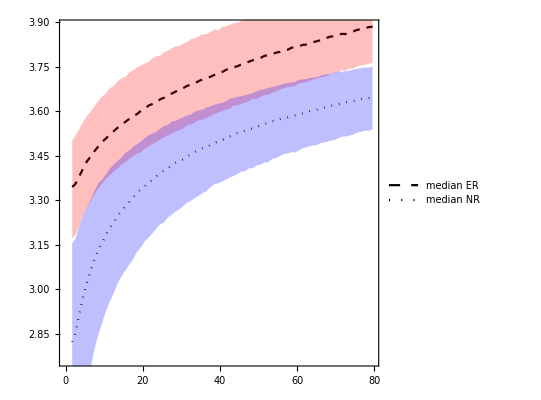

```mathematica
medians=ListPlot[{s1erMedian,s1nrMedian},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dotted}},PlotLegends->Legend[{"median ER","median NR"},LegendMarkerSize->{20,10},Position->{.8,.15}]];
bands=Show[ListPlot[{s1erDown,s1erUp},Filling->1->{2},Joined->True,FillingStyle->Opacity[.25,Red],PlotStyle->None],ListPlot[{s1nrDown,s1nrUp},Filling->1->{2},Joined->True,FillingStyle->Opacity[.25,Blue],PlotStyle->None]];
Show[medians,bands]
```

### Import detector simulation result

```mathematica
{neutronMigDat,exposure}=Import["results/S1S2_neutron_NRm_migCal_xe.dat"]//{#[[5;;-2]],#[[-1,3]]kg days}&;
```

Select out migdal and NR events:

```mathematica
neutronMigOnlyDat=Select[neutronMigDat,#[[4]]>0&];
neutronNRonlyDat=Select[neutronMigDat,#[[4]]==0&];
```

Events that pass basic cuts are about 9.4% Migdal events:

```mathematica
migRatio=Length[neutronMigOnlyDat]/Length[neutronNRonlyDat]//N
```

0.0938421

Event rate, rescaled by avg flux:

```mathematica
migRate=Length[neutronMigOnlyDat]/exposure(100/250)
```

136.931/(days kg)

#### Energy spectra

Normalized reconstructed energy spectra:

```mathematica
neutronMigOnlyDat[[1;;10]]
```

{{12.7095,4.30458,1795.17,1.46115,0.14,4,0.368334,0.105362},{56.302,3.2283,1147.15,1.0573,0.14,4,0.0858717,0.0159729},{172.821,72.5174,9986.76,8.40437,4.9,2,0.222452,0.0687575},{29.2098,2.18201,2406.02,1.2475,0.93,3,0.172917,0.0502346},{288.405,7.00474,2291.1,1.70325,0.66,3,0.0531804,0.00640401},{15.5906,4.35663,2641.67,1.17052,1.1,3,0.433293,0.114815},{18.4218,5.06586,1731.06,1.71059,0.061,4,0.240103,0.0746289},{17.6699,3.51769,3336.81,2.08082,1.1,3,0.458077,0.117707},{3.2479,3.12688,205.094,0.0324084,0.061,4,0.491842,0.121155},{48.8126,4.85579,2246.46,1.60864,0.66,3,0.131379,0.0333373}}

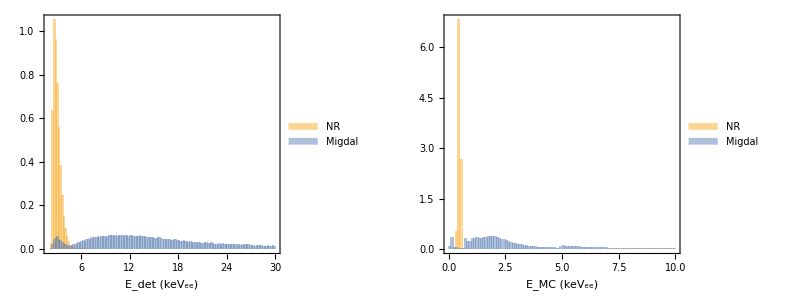

```mathematica
{{Histogram[{neutronNRonlyDat[[All,1]],neutronMigOnlyDat[[All,1]]},{2,30,.2},"PDF",FrameLabel->{"E_det (keV_ee)",""},ChartLegends->Legend[{"NR","Migdal"},Type->"Swatch"]],Histogram[{neutronNRonlyDat[[All,-2]],neutronMigOnlyDat[[All,4]]+neutronMigOnlyDat[[All,5]]+neutronMigOnlyDat[[All,-1]] neutronMigOnlyDat[[All,7]]},{0,10,.1},"PDF",FrameLabel->{"E_MC (keV_ee)",""},ChartLegends->Legend[{"NR","Migdal"},Type->"Swatch"]]}}//Grid
```

#### Angular spectra

Calculate scattering angle and append to MC data:

```mathematica
Do[neutronMigOnlyDat[[ii]]=Append[neutronMigOnlyDat[[ii]],
cosθi[neutronMigOnlyDat[[ii,7]] 10^-6,17 10^-6,(neutronMigOnlyDat[[ii,4]]+neutronMigOnlyDat[[ii,5]])10^-6,mn,131.3amu]],{ii,1,Length[neutronMigOnlyDat]}];
Do[neutronNRonlyDat[[ii]]=Append[neutronNRonlyDat[[ii]],
cosθi[neutronNRonlyDat[[ii,7]] 10^-6,17 10^-6,(neutronNRonlyDat[[ii,4]]+neutronNRonlyDat[[ii,5]])10^-6,mn,131.3amu]],{ii,1,Length[neutronNRonlyDat]}];
```

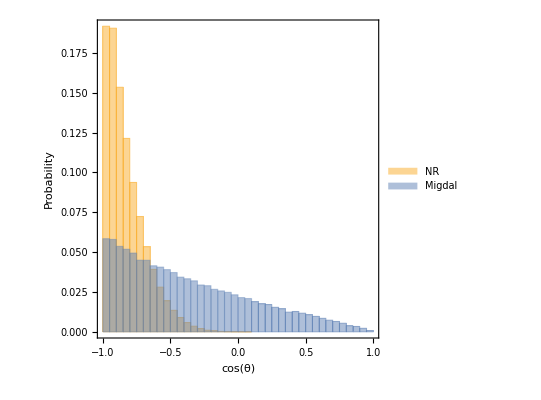

```mathematica
Histogram[{neutronNRonlyDat[[All,-1]],neutronMigOnlyDat[[All,-1]]},{-1,1,.05},"Probability",ChartLegends->Legend[{"NR","Migdal"},Type->"Swatch"],FrameLabel->{"cos(θ)","Probability"}]
```

The nuclear recoils do not appear isotropic because the detector cannot see the small E_R forward scatters. The Migdal events are more isotropically distributed though.

### Region plot

Extract S1 vs logS2 data:

```mathematica
neutronS1S2=neutronNRonlyDat//extractS1logS2;
neutronMigS1S2=neutronMigOnlyDat//extractS1logS2;
```

Bin events in S1/logS2:

```mathematica
NRbinnedS1S2=BinCounts[neutronS1S2,{2,80,1},{1,4,.1}]//Transpose;
migBinnedS1S2=BinCounts[neutronMigS1S2,{2,80,1},{1,4,.1}]//Transpose;
```

```mathematica
migVsNRplot=Show[
CredibleGridPlot2D[migBinnedS1S2,{{2,80},{1,4}},CredibleColor->Red,PlotRange->{{1,80},{2,4}},FrameLabel->{"cS1 (phd)","log_10cS2/phd"}],
CredibleGridPlot2D[NRbinnedS1S2,{{2,80},{1,4}}],
medians];
```

Credible regions with representative scatter of events:

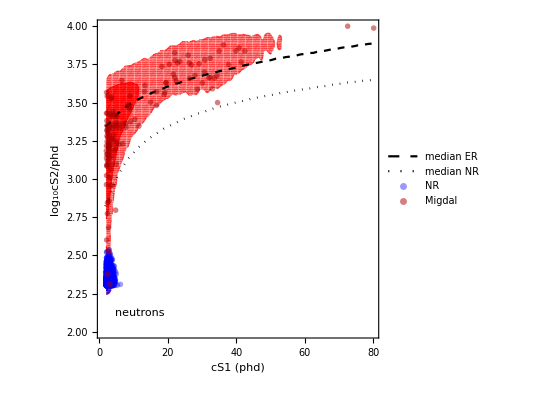

```mathematica
neutronS1S2plot=Show[migVsNRplot,
ListPlot[{neutronS1S2[[1;;Round[migRate kg days/migRatio]]],neutronMigS1S2[[1;;Round[migRate kg days]]]},ImageSize->400,
PlotStyle->{Directive[Opacity[.4,Blue],PointSize->.01],Directive[Opacity[.5,Red//Darker],PointSize->.01]},
PlotLegends->Legend[{"NR","Migdal"},Position->{.76,.31},LegendMarkerSize->15,LegendMarkers->"●"]],
Prolog->Inset[Framed[" ",FrameMargins->{{42,55},{40,50}},RoundingRadius->5,Background->White],Scaled[{.79,.24}]],
Epilog->Inset[Framed[Style["neutrons",17,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.15,.08}]]]
```

```mathematica
Export["figures/fig_xe_neutron_S1S2.pdf",Rasterize[neutronS1S2plot,ImageResolution->500]];
```

## Appendix: neutron capture

### Set up differential equations for abundance

While source is on, radiative capture occurs and the number of unstable nuclei will be increased linearly, decaying with various half lives:
dR/dt= σ ϕ N_stable
dN/dt= σ ϕ N_stable-λ N(t)

All possible transitions:

```mathematica
Nxe137[T_]=(σNC136 Φreactor Nxe136 (1 - Exp[-T λt137]))/λt137;
Nxe135[T_]=(σNC134 Φreactor Nxe134 (1 - Exp[-T λt135]))/λt135;
Nxe133[T_]=(σNC132 Φreactor Nxe132 (1 - Exp[-T λt133]))/λt133;
Nxe127[T_]=(σNC126 Φreactor Nxe126 (1 - Exp[-T λt133]))/λt133;
Nxe125[T_]=(σNC124 Φreactor Nxe124 (1 - Exp[-T λt125]))/λt125;

(*Neutron capture cross sections*)
σNC136=xeNCCS[[9]][Eneutron/eV] 10^-24 Centimeter^2;
σNC134=xeNCCS[[8]][Eneutron/eV] 10^-24 Centimeter^2;
σNC132=xeNCCS[[7]][Eneutron/eV] 10^-24 Centimeter^2;
σNC131=xeNCCS[[6]][Eneutron/eV] 10^-24 Centimeter^2;
σNC130=xeNCCS[[5]][Eneutron/eV] 10^-24 Centimeter^2;
σNC129=xeNCCS[[4]][Eneutron/eV] 10^-24 Centimeter^2;
σNC128=xeNCCS[[3]][Eneutron/eV] 10^-24 Centimeter^2;
σNC126=xeNCCS[[2]][Eneutron/eV] 10^-24 Centimeter^2;
σNC124=xeNCCS[[1]][Eneutron/eV] 10^-24 Centimeter^2;
(*Decay constants*)
λt137=Log[2]/(3.818 60 Second);
λt135=Log[2]/(9.14 3600 Second);
λt133=Log[2]/(5.247 24 3600 Second);
λt127=Log[2]/(36.35 24 3600 Second);
λt125=Log[2]/(16.9 3600 Second);
(*Number densities*)
Natoms=fidMass/MtXe Kilogram/kg;
Nxe136=isoFrac⟦9⟧Natoms;
Nxe134=isoFrac⟦8⟧Natoms;
Nxe132=isoFrac⟦7⟧Natoms;
Nxe131=isoFrac⟦6⟧Natoms;
Nxe130=isoFrac⟦5⟧Natoms;
Nxe129=isoFrac⟦4⟧Natoms;
Nxe128=isoFrac⟦3⟧Natoms;
Nxe126=isoFrac⟦2⟧Natoms;
Nxe124=isoFrac⟦1⟧Natoms;
NxeIso={Nxe124,Nxe126,Nxe128,Nxe129,Nxe130,Nxe131,Nxe132,Nxe134,Nxe136};
σNCxeIso={σNC124,σNC126,σNC128,σNC129,σNC130,σNC131,σNC132,σNC134,σNC136};
```

Total neutron capture rate:

```mathematica
Φreactor Plus@@(NxeIso σNCxeIso)Second/s
```

1962.34/s

Abundance of unstable xenon isotopes reaches a steady state after ~100 hours:

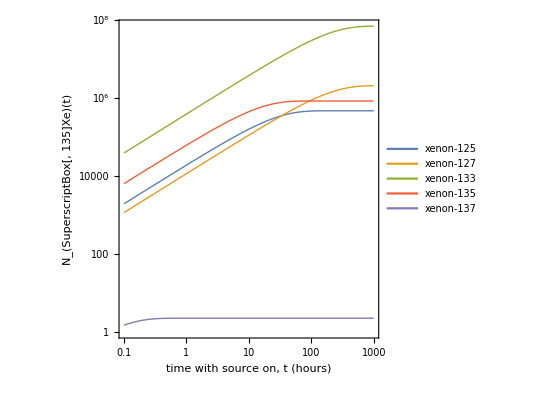

```mathematica
LogLogPlot[{Nxe125[T 3600Second],Nxe127[T 3600Second],
Nxe133[T 3600Second],Nxe135[T 3600Second],
Nxe137[T 3600Second]},{T,.1,1000},
PlotLegends->Legend[{"xenon-125","xenon-127","xenon-133","xenon-135","xenon-137"},Position->{.75,.3},LegendFunction->(Framed[#,RoundingRadius->4]&)],
FrameLabel->{"time with source on, t (hours)","N_(SuperscriptBox[, 135]Xe)(t)"},
FrameTicks->{LogTicks[10^-4,10^10],LogTicks[10^-4,10^3]}]
```

### Radiative decay spectra

Gamma data from PGAA database: https://www-nds.iaea.org/pgaa/pgaa7/index2.htm

```mathematica
xePGAAdat=Import["data/xe_pgaa.dat"]//Drop[#,1]&;
```

I believe this is evaluated at E_n = 0.05 eV, though the total cross section of these partials gives a much smaller number:

```mathematica
Plus@@xePGAAdat[[All,5]]
```

23.7317

```mathematica
Sum[xeNCCS[[ii]][.05],{ii,Length[isotopesXe]}]
```

203.906

Assume the branching ratios stay the same and scale (this seems reasonable because the capture rate is sensitive to the neutron energy, but the decay process is set by nuclear structure, adding 17keV of energy to the system is small compared to .1-10MeV  energy released in the decay).

```mathematica
xeRNCpromptSpec={};
Do[If[xePGAAdat[[i,7]]=="p",
iIso=Position[isotopesXe,xePGAAdat[[i,4]]]⟦1,1⟧;
xeRNCpromptSpec=Append[xeRNCpromptSpec,{xePGAAdat[[i,2]],
Φreactor NxeIso⟦iIso⟧xePGAAdat[[i,5]]/(xeNCCS[[iIso]][.05]) σNCxeIso[[iIso]]Second}];],
{i,1,Length[xePGAAdat]}];
xeRNCdelaySpec={};
Do[If[xePGAAdat[[i,7]]=="d",
iIso=Position[isotopesXe,xePGAAdat[[i,4]]]⟦1,1⟧;
xeRNCdelaySpec=Append[xeRNCdelaySpec,{xePGAAdat[[i,2]],
Φreactor NxeIso⟦iIso⟧xePGAAdat[[i,5]]/(xeNCCS[[iIso]][.05]) σNCxeIso[[iIso]]Second}];],
{i,1,Length[xePGAAdat]}];
```

```mathematica
gammEnergyPlot=ListLogLogPlot[{xeRNCpromptSpec,xeRNCdelaySpec},Filling->Bottom,ImageSize->400,
FillingStyle->Thick,PlotMarkers->"",PlotStyle->{Blue//Lighter,Red//Lighter},
PlotLegends->Legend[{"prompt","delayed"},Position->{.18,.85},LegendMarkerSize->8,LegendMarkers->"●",LegendFunction->(Framed[#,RoundingRadius->4]&)],
FrameLabel->{"Photon energy, E_γ (keV)","Rate (s^-1)"},
FrameTicks->{LogTicks[10^-9,10^5,2],LogTicks[10^0,10^4]}]
```

-Graphics-

```mathematica
Export["figures/fig_xe_rad_NC.pdf",gammEnergyPlot];
```

#### Transparency of xenon to gamma rays (augments position dependence)

```mathematica
xeγCS=Import["data/xe_photon_CS.dat"]//Drop[#,4]&;
```

```mathematica
xeγCS[[All,1]]*=10^3;
xeγCS[[All,2;;8]]*=ρXe(cm^3/g);
```

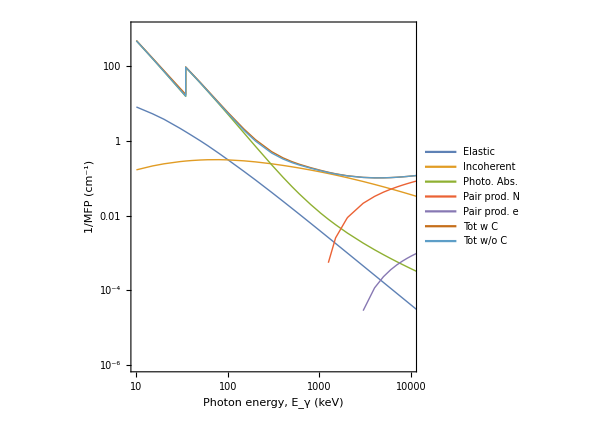

```mathematica
ListLogLogPlot[{xeγCS[[All,{1,2}]],xeγCS[[All,{1,3}]],xeγCS[[All,{1,4}]],xeγCS[[All,{1,5}]],xeγCS[[All,{1,6}]],xeγCS[[All,{1,7}]],xeγCS[[All,{1,8}]]},Joined->True,PlotRange->{{10,10^4},{10^-6,10^3}},
PlotLegends->Legend[{"Elastic","Incoherent","Photo. Abs.","Pair prod. N","Pair prod. e","Tot w C","Tot w/o C"},Position->{.2,.3},LegendFunction->"Frame"],
FrameLabel->{"Photon energy, E_γ (keV)","1/MFP (cm^-1)"},
FrameTicks->{LogTicks[10^-6,10^5],LogTicks[10^0,10^4]}]
```

Incoherent = Compton

Position resolution of XENON100 was 3mm (0.3mm 1σ) in z-direction (arxiv:1107.2155)

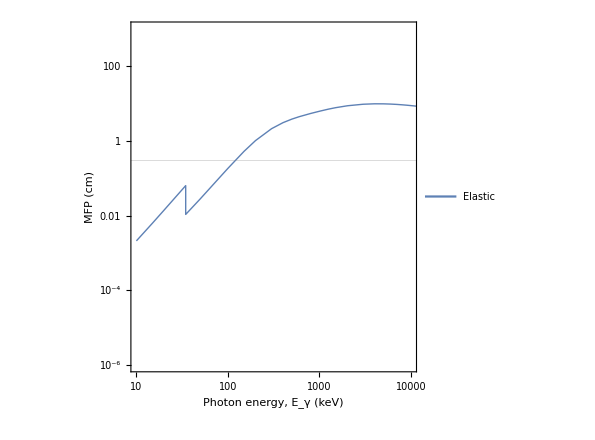

```mathematica
ListLogLogPlot[{xeγCS[[All,1]],1/xeγCS[[All,8]]}//Thread,Joined->True,PlotRange->{{10,10^4},{10^-6,10^3}},
PlotLegends->Legend[{"Elastic","Incoherent","Photo. Abs.","Pair prod. N","Pair prod. e","Tot w C","Tot w/o C"},Position->{.2,.3},LegendFunction->"Frame"],GridLines->{None,{.3}},
FrameLabel->{"Photon energy, E_γ (keV)","MFP (cm)"},
FrameTicks->{LogTicks[10^-6,10^5],LogTicks[10^0,10^4]}]
```

### Beta decay

xenon-133 beta decays to cesium-133 (stable)
xenon-135 beta decays to cesium-135 (half life ~10^6 years → ignore subsequent decay)
xenon-137 beta decays to cesium-137 (half life 30 years → ignore subsequent decay)

The rates are multiplied by the fraction of xenon within fiducial volume because we assume the xenon is constantly circulated:

```mathematica
fidFrac=0.5;
```

β-decay rate over time:

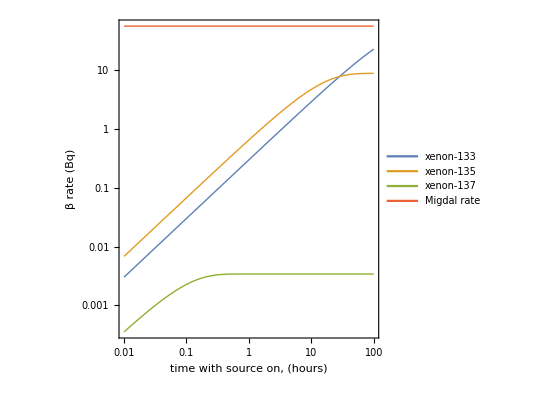

```mathematica
LogLogPlot[{fidFrac λt133 Nxe133[T 3600Second]Second,
fidFrac λt135 Nxe135[T 3600Second]Second,
fidFrac λt137 Nxe137[T 3600Second]Second,migRate (10kg days)/24},{T,.01,100},
FrameLabel->{"time with source on, (hours)","β rate (Bq)"},
PlotLegends->Legend[{"xenon-133","xenon-135","xenon-137","Migdal rate"},Position->{.2,.82},LegendFunction->"Frame"],
FrameTicks->{LogTicks[10^-4,10^3],LogTicks[10^-3,10^3]}]
```

#### Beta decay spectra

From X. Mougeot, Physical Review C 91, 055504

```mathematica
betaXe133=Import["data/xe133_beta.dat"][[All,{1,2}]];
{{betaXe135=Import["data/xe135_beta.dat"][[All,{1,2}]];}, {betaXe137=Import["data/xe137_beta.dat"][[All,{1,2}]];}}
```

{{Null},{Null}}

Convert units:

```mathematica
betaXe133[[All,1]]*=keV;
betaXe135[[All,1]]*=keV;
betaXe137[[All,1]]*=keV;
betaXe133[[All,2]]/=keV;
betaXe135[[All,2]]/=keV;
betaXe137[[All,2]]/=keV;
```

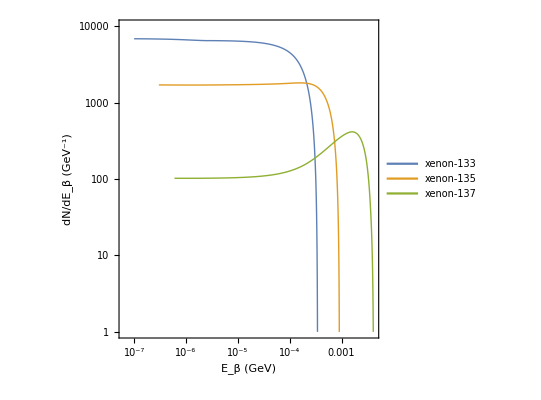

```mathematica
ListLogLogPlot[{betaXe133,betaXe135,betaXe137},Joined->True,PlotRange->{10^0,10^4},
PlotLegends->Legend[{"xenon-133","xenon-135","xenon-137"},Position->{.2,.15},LegendFunction->"Frame"],
FrameLabel->{"E_β (GeV)","dN/dE_β (GeV^-1)"},ImageSize->400,
FrameTicks->{LogTicks[10^-4,10^4],LogTicks[10^-6,10^4]}]
```

Convert to energy weighted spectra:

```mathematica
betaXe133[[All,2]]*=betaXe133[[All,1]];
betaXe135[[All,2]]*=betaXe135[[All,1]];
betaXe137[[All,2]]*=betaXe137[[All,1]];
```

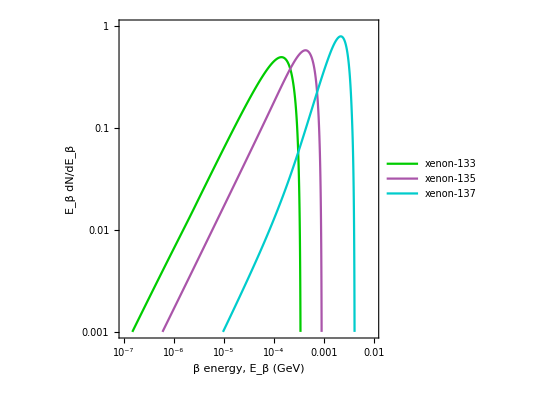

```mathematica
betaSpectra=ListLogLogPlot[{betaXe133,betaXe135,betaXe137},Joined->True,
PlotRange->{{10^-7,10^-2},{10^-3,10^0}},PlotStyle->{Darker[Green,.2],Purple//Lighter,Darker[Cyan,.2]},
PlotLegends->Legend[{"xenon-133","xenon-135","xenon-137"},Position->{.22,.83},LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&)],
FrameLabel->{"β energy, E_β (GeV)","E_β dN/dE_β"},ImageSize->400,
FrameTicks->{LogTicks[10^-4,10^4],LogTicks[10^-6,10^4]}]
```

```mathematica
Export["figures/fig_xe_beta_spectra.pdf",betaSpectra];
```

### Electron capture rates

Following EC there is atomic de-excitation: Auger decay and characteristic x-rays that could mimic a Migdal event, but also γ-rays from the nucleus which can be used as a veto.

xenon-125 ECs to iodine-125 with half-life 16.9 hours (EC is 99.82% of the time, the other 0.18% is β^+)
→ iodine-125 then EC with half-life 59.4 days (can probably ignore)

xenon-127 ECs to iodine-127 which gamma decays to it’s ground state

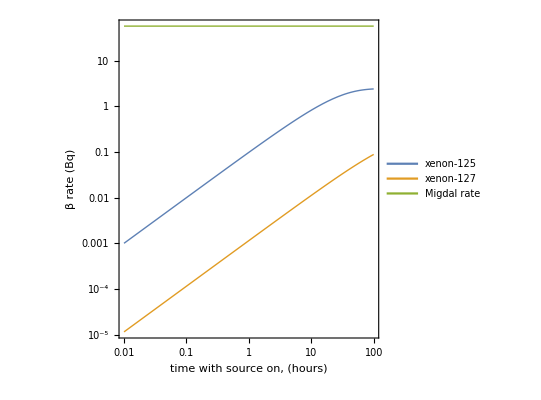

```mathematica
LogLogPlot[{fidFrac λt125 Nxe125[T 3600Second]Second,
fidFrac λt127 Nxe127[T 3600Second]Second,migRate (10kg days)/24},{T,.01,100},
FrameLabel->{"time with source on, (hours)","β rate (Bq)"},
PlotLegends->Legend[{"xenon-125","xenon-127","Migdal rate"},Position->{.8,.15},LegendFunction->"Frame"],
FrameTicks->{LogTicks[10^-4,10^3],LogTicks[10^-3,10^3]}]
```

### Combined decay-rate plot

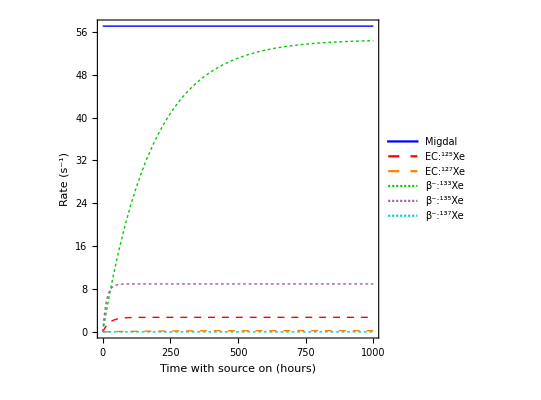
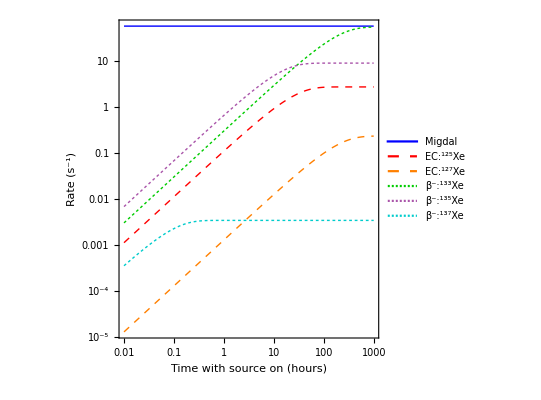

```mathematica
{decayPlot,LogDecayPlot}={Plot[{
migRate (10kg days)/24,
fidFrac λt125 Nxe125[T 3600Second]Second,
fidFrac λt127 Nxe127[T 3600Second]Second,
fidFrac λt133 Nxe133[T 3600Second]Second,
fidFrac λt135 Nxe135[T 3600Second]Second,
fidFrac λt137 Nxe137[T 3600Second]Second
},{T,.01,10^3},ImageSize->400,
FrameLabel->{"Time with source on (hours)","Rate (s^-1)"},
PlotStyle->{{Blue,Thick},{Red,Thick,Dashed},{Orange,Thick,Dashed},{Darker[Green,.2],Thick,Dashing[{.005,.005}]},{Purple//Lighter,Thick,Dashing[{.005,.005}]},{Darker[Cyan,.2],Thick,Dashing[{.005,.005}]}},
PlotLegends->Legend[{"Migdal","EC:^125Xe","EC:^127Xe ","β^-:^133Xe","β^-:^135Xe","β^-:^137Xe"},Position->{.78,.5},
LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&)]],LogLogPlot[{
migRate (10kg days)/24,
fidFrac λt125 Nxe125[T 3600Second]Second,
fidFrac λt127 Nxe127[T 3600Second]Second,
fidFrac λt133 Nxe133[T 3600Second]Second,
fidFrac λt135 Nxe135[T 3600Second]Second,
fidFrac λt137 Nxe137[T 3600Second]Second
},{T,.01,10^3},ImageSize->400,
FrameLabel->{"Time with source on (hours)","Rate (s^-1)"},
PlotStyle->{{Blue,Thick},{Red,Thick,Dashed},{Orange,Thick,Dashed},{Darker[Green,.2],Thick,Dashing[{.005,.005}]},{Purple//Lighter,Thick,Dashing[{.005,.005}]},{Darker[Cyan,.2],Thick,Dashing[{.005,.005}]}},
PlotLegends->Legend[{"Migdal","EC:^125Xe","EC:^127Xe ","β^-:^133Xe","β^-:^135Xe","β^-:^137Xe"},Position->{.78,.27},
LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&)],
FrameTicks->{LogTicks[10^-5,10^3],LogTicks[10^-3,10^3]}]}
```

```mathematica
Export["figures/fig_xe_decay_plot.pdf",LogDecayPlot];
```

### Background simulation in NEST

#### Gammas

Import NEST simulation of gamma decays **these are not indicative of actual rate since Compton scattering will dominate for higher energy gammas** this requires more detailed simulations and so won’t appear in the paper.

```mathematica
xeRNCpromptDat=Import["results/S1S2_RNCprompt_ER_migTest_xe.dat"][[5;;-2]];
```

```mathematica
xeRNCpromptRatio=Import["results/S1S2_RNCprompt_ER_migTest_xe.dat"][[-1,4]]
```

0.637201

```mathematica
xeRNCpromptBinnedS1S2=BinCounts[xeRNCpromptDat//extractS1logS2,{1200,12000,100},{4,6,.1}]//Transpose;
```

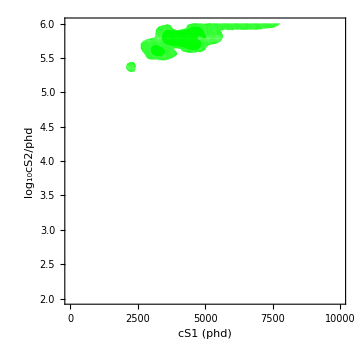

```mathematica
CredibleGridPlot2D[xeRNCpromptBinnedS1S2,{{1200,12000},{4,6}},CredibleColor->Green,PlotRange->{{1,10000},{2,6}},FrameLabel->{"cS1 (phd)","log_10cS2/phd"}]
```

#### Betas

Import NEST simulation of beta decays:

```mathematica
NotebookDirectory[]//SetDirectory;
xe133betaDat=Import["results/S1S2_xe133beta_ER_migCalFull_xe.dat"][[5;;-2]];
xe135betaDat=Import["results/S1S2_xe135beta_ER_migCalFull_xe.dat"][[5;;-2]];
xe137betaDat=Import["results/S1S2_xe137beta_ER_migCalFull_xe.dat"][[5;;-2]];
```

```mathematica
xe133betaTrials=Import["results/S1S2_xe133beta_ER_migCalFull_xe.dat"][[-1,3]];
xe135betaTrials=Import["results/S1S2_xe135beta_ER_migCalFull_xe.dat"][[-1,3]];
xe137betaTrials=Import["results/S1S2_xe137beta_ER_migCalFull_xe.dat"][[-1,3]];
```

```mathematica
xe133betaBinnedS1S2=BinCounts[xe133betaDat//extractS1logS2,{2,xe133betaDat[[All,2]]//Max,6},{2.5,6,.1}]//Transpose;
xe135betaBinnedS1S2=BinCounts[xe135betaDat//extractS1logS2,{2,xe135betaDat[[All,2]]//Max,8},{2.5,6,.1}]//Transpose;
xe137betaBinnedS1S2=BinCounts[xe137betaDat//extractS1logS2,{2,xe137betaDat[[All,2]]//Max,10},{2.5,6,.1}]//Transpose;
```

```mathematica
beta137S1S2plot=CredibleGridPlot2D[xe137betaBinnedS1S2,{{2,xe137betaDat[[All,2]]//Max},{2.5,6}},CredibleColor->Red,FrameLabel->{"cS1 (phd)","log_10cS2/phd"}]
```

-Graphics-

```mathematica
beta135S1S2plot=CredibleGridPlot2D[xe135betaBinnedS1S2,{{2,xe135betaDat[[All,2]]//Max},{2.5,6}},CredibleColor->Purple,FrameLabel->{"cS1 (phd)","log_10cS2/phd"}]
```

-Graphics-

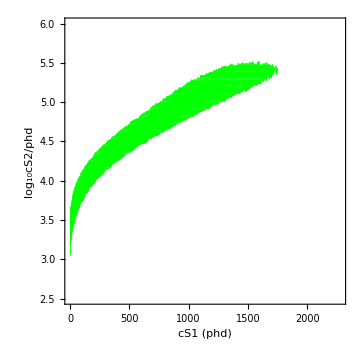

```mathematica
beta133S1S2plot=CredibleGridPlot2D[xe133betaBinnedS1S2,{{2,xe133betaDat[[All,2]]//Max},{2.5,6}},CredibleColor->Green,FrameLabel->{"cS1 (phd)","log_10cS2/phd"}]
```

```mathematica
combinedBetaS1S2plot=Show[
CredibleGridPlot2D[migBinnedS1S2,{{2,80},{1,4}},CredibleColor->Red,PlotRange->{{1,80},{2,4}},FrameLabel->{"cS1 (phd)","log_10cS2/phd"},
Prolog->Inset[Framed[" ",FrameMargins->{{44,55},{50,76}},RoundingRadius->5,Background->White],Scaled[{.79,.31}]],Epilog->Inset[Framed[Style[" "],RoundingRadius->4,FrameMargins->{{35,65},{55,55}}],Scaled[{.82,.2}]]],
CredibleGridPlot2D[NRbinnedS1S2,{{2,80},{1,4}}],
medians,beta133S1S2plot/.Green->Darker[Green,.2],
ListPlot[{neutronS1S2[[1;;Round[migRate kg days/migRatio]]],neutronMigS1S2[[1;;Round[migRate kg days]]],extractS1logS2[xe133betaDat]⟦1;;Round[fidFrac λt133 Nxe133[10^3 3600Second]Second]⟧},ImageSize->400,
PlotStyle->{Directive[Opacity[.4,Blue],PointSize->.01],Directive[Opacity[.5,Red//Darker],PointSize->.01],Directive[Opacity[.5,Green//Darker],PointSize->.01]},
PlotLegends->Legend[{"NR","Migdal","β^-:^133Xe"},Position->{.75,.4},LegendMarkerSize->20,LegendMarkers->"●"]],Epilog->Inset[Framed[Style["neutrons",17,FontFamily->"Times"],RoundingRadius->5,Background->White],Scaled[{.15,.08}]]]
```

-Graphics-

```mathematica
Export["figures/fig_xe_beta_S1S2.png",Rasterize[combinedBetaS1S2plot,ImageResolution->400]];
```

These plots show that the β decays can have much higher energies and only a small fraction will be in our analysis window:

```mathematica
maxS1=50;
maxLogS2=4;
```

Perform cut and extract S1-logS2

```mathematica
xe133s1s2=xe133betaDat//Select[#,#[[2]]<60&]&//Select[#,#[[3]]<10^4&]&//extractS1logS2;
xe135s1s2=xe135betaDat//Select[#,#[[2]]<60&]&//Select[#,#[[3]]<10^4&]&//extractS1logS2;
xe137s1s2=xe137betaDat//Select[#,#[[2]]<60&]&//Select[#,#[[3]]<10^4&]&//extractS1logS2;
```

Fraction of events passing cuts:

```mathematica
xe133betaFrac=Length[xe133s1s2]/xe133betaTrials//N;
xe135betaFrac=Length[xe135s1s2]/xe135betaTrials//N;
xe137betaFrac=Length[xe137s1s2]/xe137betaTrials//N;
{xe133betaFrac,xe135betaFrac,xe137betaFrac}
```

{0.0502448,0.0131806,0.000818646}

Number of events which pass cuts as function of running time:

```mathematica
totβBG[hoursOn_]=fidFrac Integrate[xe133betaFrac λt133 Nxe133[T 3600Second]Second+xe135betaFrac λt135 Nxe135[T 3600Second]Second+xe137betaFrac λt137 Nxe137[T 3600Second]Second,{T,0,hoursOn}];
```

Number of EC events assuming no cuts (need to improve on this, but it is pessimistic for now):

```mathematica
totECBG[hoursOn_]=fidFrac Integrate[λt125 Nxe125[T 3600Second]Second+λt127 Nxe127[T 3600Second]Second,{T,0,hoursOn}];
```

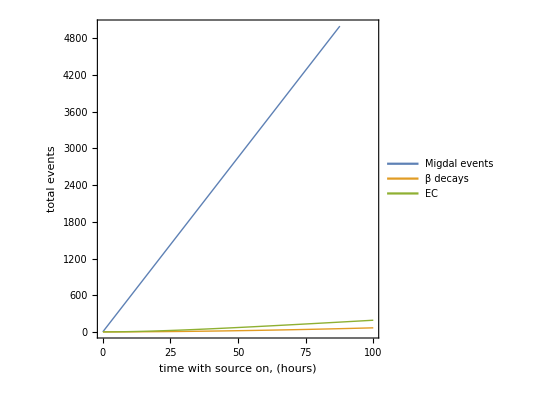
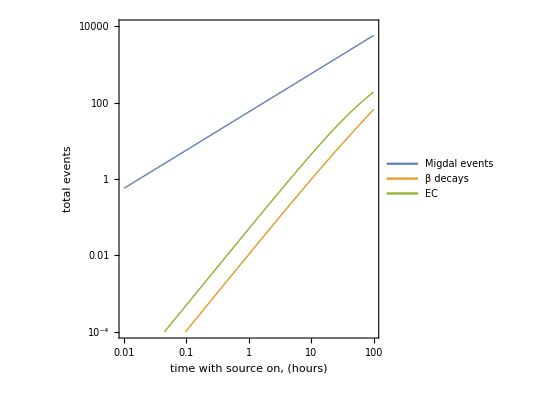

```mathematica
{Plot[{(migRate 10kg days) hoursOn/24,totβBG[hoursOn],totECBG[hoursOn]},{hoursOn,.01,100},
FrameLabel->{"time with source on, (hours)","total events"},ImageSize->400,PlotRange->{10^-4,5000},
PlotLegends->Legend[{"Migdal events","β decays","EC"},Position->{.22,.86},LegendFunction->"Frame"]],LogLogPlot[{(migRate 10kg days) hoursOn/24,totβBG[hoursOn],totECBG[hoursOn]},{hoursOn,.01,100},
FrameLabel->{"time with source on, (hours)","total events"},ImageSize->400,PlotRange->{10^-4,10^4},
PlotLegends->Legend[{"Migdal events","β decays","EC"},Position->{.22,.86},LegendFunction->"Frame"],
FrameTicks->{LogTicks[10^-4,10^4],LogTicks[10^-3,10^3]}]}
```

After 24 hours we will have (in ROI):

```mathematica
migRate (10kg) (1days )
```

1369.31

```mathematica
totβBG[24]
```

5.11927

```mathematica
totECBG[24]
```

21.6467